```mathematica
plotData[file_,withElephant_,sizes_]:=Module[{str,listStrings,missCount,outOfOrder,sum,l,x},(
str = Import[file];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];
outOfOrder = ToExpression[ StringDrop[listStrings[[2]],{-3}]];



sum = Total[Map[#[[3]]&,missCount]];
data = Map[{#[[1]],100*#[[2]],#[[3]]}&,outOfOrder];
d=Map[Module[{s},s=Floor[#];Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,sizes];
(*The miss count:*)
missCountList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,missCount];
If[withElephant == True,rtt = (5.8)*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt;
missHopPlots = Map[Module[{s,oneSzie,oneSum,oneMean},s=Floor[#];
oneSzie = Select[missCount,(#[[1]]==s)&];
oneSum = Total[Map[#[[3]]&,oneSzie]];
oneMean = N[Total[Map[#[[4]]&,oneSzie]]/oneSum];
Labeled[ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT\nrate = " <> ToString[pivot/10^6] <> " Mbps",Tiny],Automatic]}],"Avg miss hop = " <> ToString[oneMean]]
]&,sizes];
Return[{missHopPlots,N[Total[Map[#[[4]]&,missCount]]/sum]}];

(*Size distribution validation:*)
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}]];
Print[BarChart[N[1/Total[d]*d],ChartLabels->sizes,PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]];
Print[ListPlot3D[missCountList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Miss count",AxesLabel->{"size (Bytes)","rate (Mbps)","miss count"},PlotRange->{0,4}]];
Print["The mean of the miss count: ",N[Total[Map[#[[4]]&,missCount]]/sum]];


Print[missHopPlots];
Print[Total[missHopPlots]];

hashsize[size_]:=Position[sizes,size][[1]][[1]];
heatMap = ConstantArray[0,{17,40000/100}];
Map[((heatMap[[hashsize[#[[1]]],(#[[2]])/100]] = #[[3]]))&,data3];

outOfOrderList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,outOfOrder];
Print[ListPlot3D[outOfOrderList,Mesh->None,InterpolationOrder->0,PlotLabel->"Avg Out of order",AxesLabel->{"size (Bytes)","rate (Mbps)","out of oreder"},PlotRange->All]];
Print[Map[Module[{s},s=#;ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[outOfOrderList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s],AxesLabel->{"Rate (Mbps)","Avg out of order"}]]&,sizes]];

Print["The mean of the out of oreder: ",N[Total[Map[(#[[4]])/sum&,outOfOrder]]]];
)];

sizeDistributionValidationI[file_,sizes_]:=Module[{str,listStrings,missCount,data,probs,d},(
str = Import[file];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];


data = Map[{#[[1]],100*#[[2]],#[[3]]}&,missCount];
d=Map[Module[{s},s=Floor[#];Round[Total[Map[#[[3]]&,Select[data,(#[[1]]==s)&]]]/(s/1500)]]&,DeleteDuplicates[data[[All,1]]]];
d = N[1/Total[d]*d];
probs = Switch[sizes,sizesHadoop,distOfSizesHadoop,sizesWebSearch,distOfSizesWebSearch,sizesDataMining,distOfSizesDataMining];
Grid[{{BarChart[Table[Tooltip[probs[[i]],"size = "<>ToString[sizes[[i]]]<>" , p = "<>ToString[probs[[i]]]],{i,Length[probs]}],PlotLabel->"The real distribution of sizes",AxesLabel->{"size","PDF"}],BarChart[Table[Tooltip[d[[i]],"size = "<>ToString[sizes[[i]]]<>" , p = "<>ToString[d[[i]]]],{i,Length[d]}],PlotLabel->"Distribution of sizes in the simulation",AxesLabel->{"size","PDF"}]}}])];
missCountAvg[file_]:=Module[{FileAsList,indexOfMissCount},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.dest \"miss count\""][[1]][[1]];
ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 2]]]]])];

getPercentageOfTrafficToController[file_]:=Module[{FileAsList,indexOfMissCount,indexLineController},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.dest \"miss count\""][[1]][[1]];
indexLineController = 0;
While[!StringContainsQ[FileAsList[[indexOfMissCount + indexLineController]],"bin\t2"],indexLineController+=1];
N[ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + indexLineController]]]]]/ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 1]]]]]]
)];

getPercentageOfTrafficToComponent[file_,i_]:=Module[{FileAsList,indexOfMissCount,indexOfComponent},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.dest \"miss count\""][[1]][[1]];
indexOfComponent =Select[Range[5,30],(StringContainsQ[FileAsList[[indexOfMissCount+#]],"bin	"<>ToString[i]<>"	"])&][[1]];
N[ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + indexOfComponent]]]]]/ToExpression[Last[StringSplit[FileAsList[[indexOfMissCount + 1]]]]]])];

getLifeTimeOfARule[file_]:=Module[{FileAsList,indexOfMissCount,l},(
FileAsList = Import[file,"List"];
indexOfMissCount = Position[FileAsList,"statistic Network.agg[0] life_time_of_a_rule"][[1]][[1]];
l=StringSplit[Last[StringSplit[FileAsList[[indexOfMissCount+2]]]],"e"];
If[Length[l]==1,N[ToExpression[l[[1]]]],N[ToExpression[l[[1]]]*10^ToExpression[l[[2]]]]]
)];

getInsertionRate[file_]:=ToExpression[Last[StringSplit[Select[Import[file,"List"],(StringContainsQ[#,"insertion_rate"])&][[1]]]]];

getOutOfOrderPercentage[file_]:=ToExpression[Last[StringSplit[Select[Import[file,"List"],(StringContainsQ[#,"Out of order percentage"])&][[1]]]]];




distributions = {"C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv"};
createDist[dist_]:=Module[{sizes,prob},(
prob = Import[dist,"Grid"][[1]][[2;;]][[All,2]];
prob={prob[[1]]}~Join~Table[prob[[i]] - prob[[i-1]],{i,2,Length[prob]}];
sizes = Import[dist,"Grid"][[1]][[2;;]][[All,1]];
Return[EmpiricalDistribution[prob->sizes]]
)];



plotResults[file_,cacheSizes_,thresholds_]:=Module[{temp,improveBandToCont,improveMissCount,thMinimalMissHop,thMinimalBand},(
Print[ListLogLinearPlot[Outer[(temp={#2,missCountAvg[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]};Tooltip[If[temp[[1]]==0,{thresholds[[2]]/1.2(*Where to show the point of 0*),temp[[2]]},temp],temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]&,cacheSizes],Joined->True,AxesLabel->{"threshold (rate)","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]];
Print[ListLogLinearPlot[Outer[(temp={#2,getPercentageOfTrafficToController[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]};Tooltip[If[temp[[1]]==0,{thresholds[[2]]/1.2(*Where to show the point of 0*),temp[[2]]},temp],temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]&,cacheSizes],Joined->True,AxesLabel->{"threshold (rate)","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]];





Print[Quiet[sizeDistributionValidationI[StringReplace[file,{"AAA"->ToString[cacheSizes[[1]]],"BBB"->ToString[thresholds[[1]]],"scalar-file.sca"->"Total.txt"}],sizesHadoop]]];


temp = Outer[({#2,missCountAvg[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]})&,cacheSizes,thresholds];
thMinimalMissHop =Table[MinimalBy[temp[[i]],Last][[1]][[1]],{i,1,Length[cacheSizes]}] ;
improveMissCount = Table[(1-Min[Transpose[temp[[i]]][[2]]]/Transpose[temp[[i]]][[2]][[1]])*100,{i,1,Length[cacheSizes]}];
temp = Outer[({#2,getPercentageOfTrafficToController[StringReplace[file,{"AAA"->ToString[#1],"BBB"->ToString[#2]}]]})&,cacheSizes,thresholds];
thMinimalBand =Table[MinimalBy[temp[[i]],Last][[1]][[1]],{i,1,Length[cacheSizes]}] ;
improveBandToCont = Table[(1-Min[Transpose[temp[[i]]][[2]]]/Transpose[temp[[i]]][[2]][[1]])*100,{i,1,Length[cacheSizes]}];
Print[Grid[Transpose[{{"cache size"}~Join~cacheSizes,{"Improvement in miss count (in percentages)"}~Join~improveMissCount,{"Optimal threshold by miss hop"}~Join~thMinimalMissHop,{"Improvement in bandwidth to controller (in percentages)"}~Join~improveBandToCont,{"Optimal threshold by bandwidth to controller"}~Join~thMinimalBand}],Frame->All]];
)];
```

-Graphics-

Distribution Of the rates:

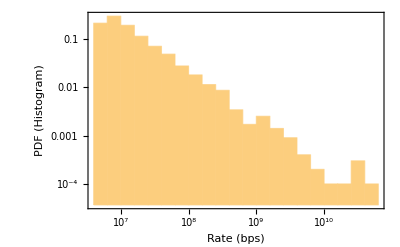

```mathematica
f[α_,β_]:=β*(1/(1-RandomVariate[UniformDistribution[{0.001,0.999}]]))^(1/α);
g[α_,β_,x_]:=Min[40*10^9,x*β*(1/(1-RandomVariate[UniformDistribution[]]))^(1/α)];
descriptivestatistics[data_]:={{"Mean","Median","Stdv.","Skewness","Kurtosis"},{Mean[data],Median[data],StandardDeviation[data],Skewness[data],Kurtosis[data]}}//Transpose//Grid//Panel;
list=Table[(
Subscript[l, i]=Table[g[1.0256410256410255,10^6,5*10^(i-1)],{j,10000}];
Subscript[h, i] = GraphicsGrid[{{Histogram[Subscript[l, i],"Log","LogProbability",FrameLabel->{"Rate (bps)","PDF (Histogram)"},Frame->True],descriptivestatistics@Subscript[l, i]}},ImageSize->Full]
),{i,1,4}];

list[[1]]
```

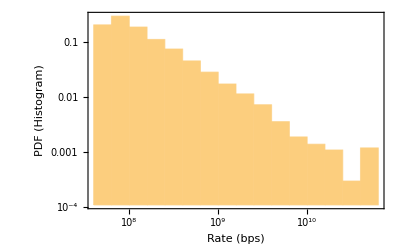

```mathematica
list[[2]]
```

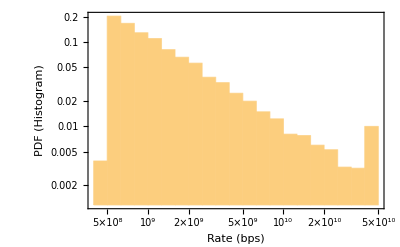

```mathematica
list[[3]]
```

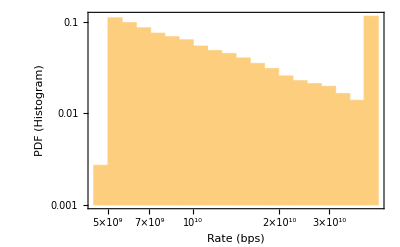

```mathematica
list[[4]]
```

Distribution Of the sizes and packet types:

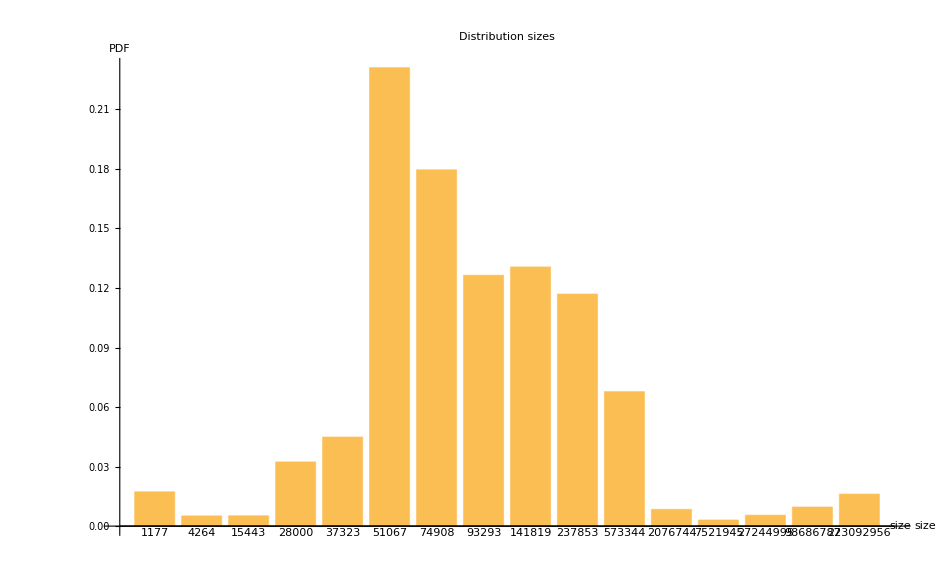

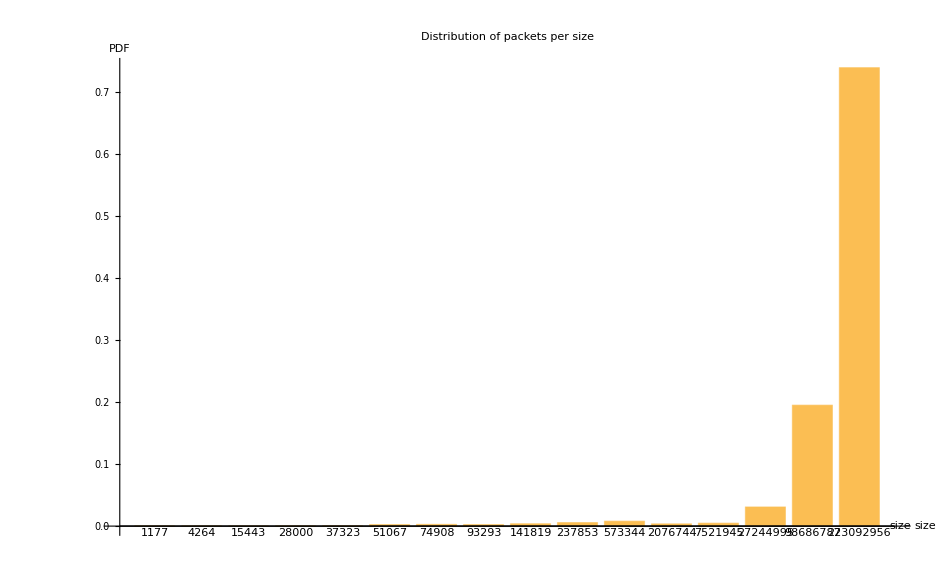

```mathematica
sizes = {1177 ,4264 ,15443 ,28000 ,37323 ,51067 ,74908 ,93293 ,141819 ,237853 ,573344 ,2076744 ,7521945 ,27244995 ,98686787 ,223092956};
distOfSizes = {0.01728594,0.005140236,0.005232129,0.032341695,0.044879491,0.231028785,0.179568695,0.126417652,0.130605671,0.116946187,0.067761784,0.008431136,0.003078399,0.005519292,0.009625739,0.016137169};
Print[BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]]

Print[BarChart[Table[N[(distOfSizes[[j]]*sizes[[j]])/Total[Table[distOfSizes[[i]]*sizes[[i]],{i,1,16}]]],{j,1,16}],ChartLabels->sizes,PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]]
```

The new distribution of the sizes:

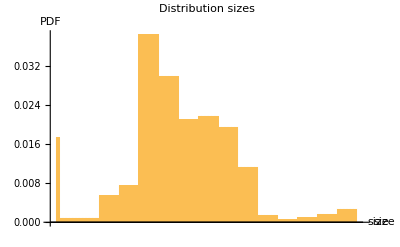
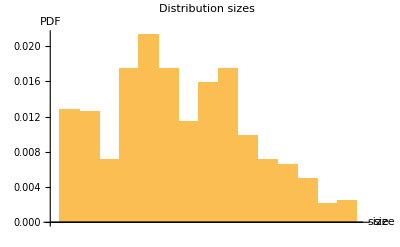
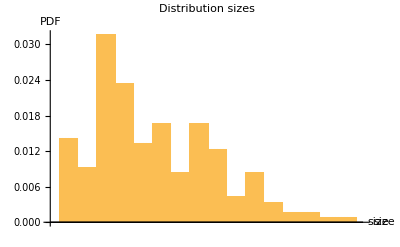
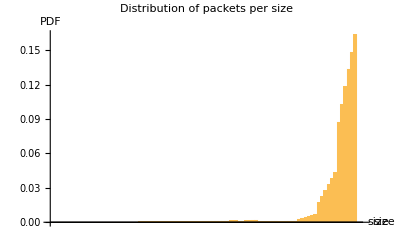
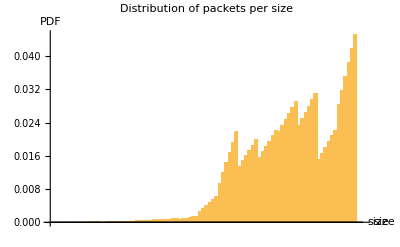
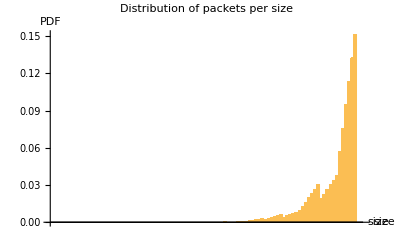
Hadoop | WebSearch | DataMining
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
3.66326×10^6 | 1.55469×10^6 | 5.50755×10^6

```mathematica
distOfSizesHadoop = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesHadoop={distOfSizesHadoop[[1]]}~Join~Table[distOfSizesHadoop[[i]] - distOfSizesHadoop[[i-1]],{i,2,Length[distOfSizesHadoop]}];
sizesHadoop = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]];

distOfSizesDataMining = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesDataMining={distOfSizesDataMining[[1]]}~Join~Table[distOfSizesDataMining[[i]] - distOfSizesDataMining[[i-1]],{i,2,Length[distOfSizesDataMining]}];
sizesDataMining = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-datamining.csv","Grid"][[1]][[2;;]][[All,1]];


distOfSizesWebSearch = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv","Grid"][[1]][[2;;]][[All,2]];
distOfSizesWebSearch={distOfSizesWebSearch[[1]]}~Join~Table[distOfSizesWebSearch[[i]] - distOfSizesWebSearch[[i-1]],{i,2,Length[distOfSizesWebSearch]}];
sizesWebSearch = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-websearch.csv","Grid"][[1]][[2;;]][[All,1]];



Grid[{{"Hadoop","WebSearch","DataMining"},{BarChart[distOfSizesHadoop,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}],BarChart[distOfSizesWebSearch,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}],BarChart[distOfSizesDataMining,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]},{BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}],BarChart[Table[N[(distOfSizesWebSearch[[j]]*sizesWebSearch[[j]] )/Total[Table[distOfSizesWebSearch[[i]]*sizesWebSearch[[i]],{i,1,Length[sizesWebSearch]}]]],{j,1,Length[sizesWebSearch]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}],BarChart[Table[N[(distOfSizesDataMining[[j]]*sizesDataMining[[j]] )/Total[Table[distOfSizesDataMining[[i]]*sizesDataMining[[i]],{i,1,Length[sizesDataMining]}]]],{j,1,Length[sizesDataMining]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]},{Total[Table[sizesHadoop[[i]]*distOfSizesHadoop[[i]],{i,1,Length[sizesHadoop]}]],Total[Table[sizesWebSearch[[i]]*distOfSizesWebSearch[[i]],{i,1,Length[sizesWebSearch]}]],Total[Table[sizesDataMining[[i]]*distOfSizesDataMining[[i]],{i,1,Length[sizesDataMining]}]]}}]


BarChart[distOfSizesHadoop,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];

BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Total[Table[sizesHadoop[[i]]*distOfSizesHadoop[[i]],{i,1,Length[sizesHadoop]}]];
```

Number of flowlets in window:

```mathematica
Subscript[list, 40]={{10,46.44561},{20,90.5256},{30,132.91443914439},{40,173.94772},{50,213.8356},{60,252.74132965319},{70,290.72943647182},{80,327.94616},{90,364.41211412114}};
Subscript[list, 400] ={{10,124.21595},{20,217.72968},{30,295.62550625506},{40,362.92448},{50,422.20425},{60,475.12048481939},{70,522.72411620581},{80,565.85456},{90,605.146}};
Subscript[list, 4000] ={{10,301.60049},{20,413.12056},{30,466.59103591036},{40,494.55032},{50,510.04655},{60,518.95721828873},{70,524.27616380819},{80,527.63152},{90,529.80847808478}};
Subscript[list, 40000] ={{10,140.30559},{20,141.39894},{30,141.91869918699},{40,142.43528},{50,142.95135},{60,143.46573862955},{70,143.98809940497},{80,144.50424},{90,145.0202502025}};

ListPlot[{Callout[Subscript[list, 40],"Mean = 40 M"],Callout[Subscript[list, 400],"Mean = 400 M"],Callout[Subscript[list, 4000],"Mean = 2.5 G"],Callout[Subscript[list, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of flowlets that seen at the window"}]
```

-Graphics-

```mathematica
Subscript[newlist, 40]={{10,4426.63962},{20,4428.44124},{30,4430.2349923499},{40,4432.05148},{50,4433.86395},{60,4435.5899435977},{70,4437.3750787539},{80,4439.26128},{90,4441.0571505715}};
Subscript[newlist, 400] ={{10,1130.41252},{20,1132.442},{30,1134.4671946719},{40,1136.50688},{50,1138.54415},{60,1140.5311412456},{70,1142.5686384319},{80,1144.62856},{90,1146.6562865629}};
Subscript[newlist, 4000] ={{10,530.49309},{20,532.81376},{30,535.14094140941},{40,542.10026401056},{50,539.78855},{60,542.10026401056},{70,544.41575078754},{80,546.75304},{90,549.09144091441}};
Subscript[newlist, 40000] ={{10,142.9596},{20,145.54734},{30,148.13356133561},{40,150.72184},{50,153.30955},{60,155.89523580943},{70,158.48925446272},{80,161.07736},{90,163.66474664747},{1000,424.6548}};

ListPlot[{Callout[Subscript[newlist, 40],"Mean = 40 M"],Callout[Subscript[newlist, 400],"Mean = 400 M"],Callout[Subscript[newlist, 4000],"Mean = 2.5 G"],Callout[Subscript[newlist, 40000],"Mean = 15 G"]},Joined->True,PlotLabel->"Number of living flowlets as a function of window size",AxesLabel->{"Window size  (μs)","Number of living flowlets"}]
```

-Graphics-

With/Without elephant Detector push = 1,2,10:

```mathematica
{q1,nav1} = plotData["with 1,1.txt",True];
{q2,nav2} = plotData["witout 1,1.txt",False];
{q3,nav3} = plotData["with 2,2.txt",True];
{q4,nav4}= plotData["without 2,2.txt",False];
{q5,nav5}= plotData["with 10,10.txt",True];
{q6,nav6}= plotData["without 10,10.txt",False];
Manipulate[{Labeled[q1[[i]],"With 1,1\n Total Avg miss hop = " <> ToString[nav1]],Labeled[q2[[i]],"Without 1,1\n Total Avg miss hop = " <> ToString[nav2]],Labeled[q3[[i]],"With 2,2\n Total Avg miss hop = " <> ToString[nav3]],Labeled[q4[[i]],"Without 2,2\n Total Avg miss hop = " <> ToString[nav4]],Labeled[q5[[i]],"With 10,10\n Total Avg miss hop = " <> ToString[nav5]],Labeled[q6[[i]],"Without 10,10\n Total Avg miss hop = " <> ToString[nav6]]},{i,1,Length[sizes],1}]
```

Set::shape: Lists {q1,nav1} and plotData[with 1,1.txt,True] are not the same shape.

Set::shape: Lists {q2,nav2} and plotData[witout 1,1.txt,False] are not the same shape.

Set::shape: Lists {q3,nav3} and plotData[with 2,2.txt,True] are not the same shape.

Set::shape: Lists {q4,nav4} and plotData[without 2,2.txt,False] are not the same shape.

Set::shape: Lists {q5,nav5} and plotData[with 10,10.txt,True] are not the same shape.

Set::shape: Lists {q6,nav6} and plotData[without 10,10.txt,False] are not the same shape.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1[[1]] is longer than depth of object.

Part::partd: Part specification q2[[1]] is longer than depth of object.

Part::partd: Part specification q3[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification q1⟦1⟧ is longer than depth of object.

Part::partd: Part specification q2⟦1⟧ is longer than depth of object.

Part::partd: Part specification q3⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Static Ideal Elephant Detector According to size:

```mathematica
Map[(Subscript[b, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull great then " <> ToString[#] <>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True,sizes])&,sizes];
```

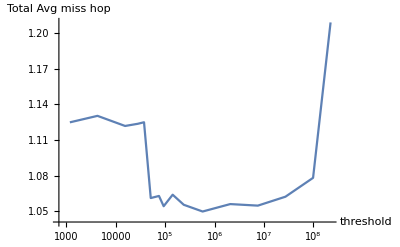

573344

```mathematica
Manipulate[Labeled[Subscript[b, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[b, flowSize][[2]]],Top],{{flowSize,sizes[[1]],"insert a flow whose size is greater than"},sizes}]
ListLogLinearPlot[Map[{#,Subscript[b, #][[2]]}&,sizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[b, #]]&,sizes],Min[Map[Last[Subscript[b, #]]&,sizes]]][[1]][[1]]]]
```

Dynamic Elephant Detector According to Hit Ratio (Local/Total)Threshold =   size:

```mathematica
reset= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\\4.09999999999999964473  -  4.20000000000000017764.txt",True];
nonReset = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\\4.09999999999999964473  -  4.20000000000000017764.txt",True];
```

```mathematica
Manipulate[{Labeled[reset[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[reset[[2]]],Top],Labeled[nonReset[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[nonReset[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]
```

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\4.09999999999999964473  -  4.20000000000000017764.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\4.09999999999999964473  -  4.20000000000000017764.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset[[1]] is longer than depth of object.

Part::partd: Part specification reset[[2]] is longer than depth of object.

Part::partd: Part specification nonReset[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ToExpression::sntx: Invalid syntax in or before "General-0-20221224-11:30:19-5128".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221224-11:30:19".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "ratio/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

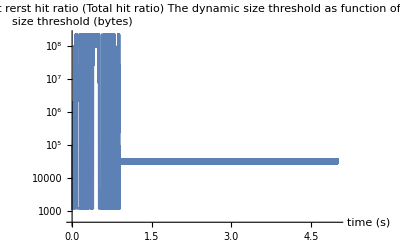

The maximum threshold after 1s is 37323
The minimum threshold after 1s is 28000

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning non reset hit ratio\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"Without rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221224-11:31:23-18328".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221224-11:31:23".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "ratio/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

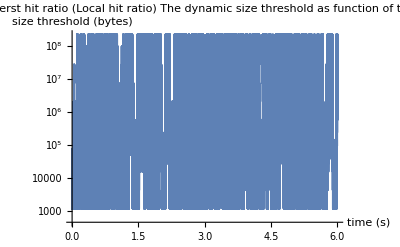

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull self learning reset hit ratio\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"With rerst hit ratio (Local hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-08:39:09-12308".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-08:39:09".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

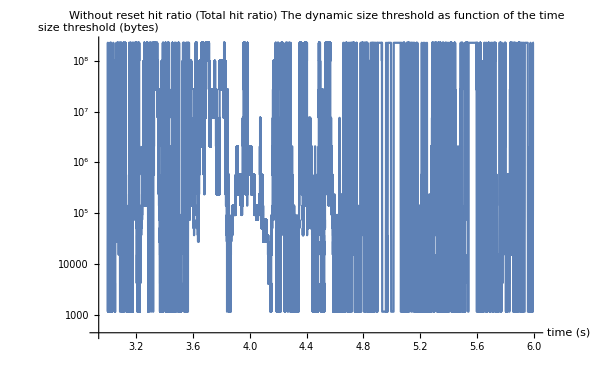

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-08:39:44-8252".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-08:39:44".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

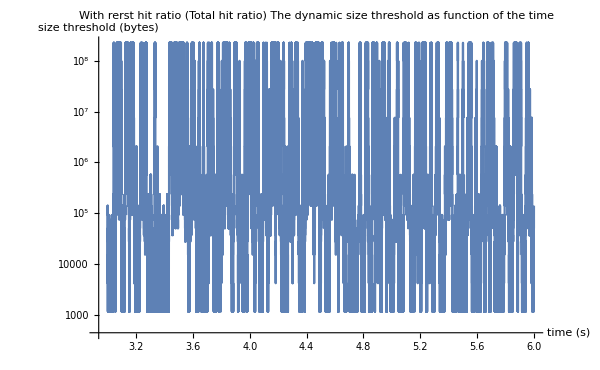

The maximum threshold after 1s is 223092956
The minimum threshold after 1s is 1177

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf dynamic non reset\5.50000000000000000000  -  6.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf dynamic with reset\5.50000000000000000000  -  6.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification reset1[[1]] is longer than depth of object.

Part::partd: Part specification reset1[[2]] is longer than depth of object.

Part::partd: Part specification nonReset1[[1]] is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification reset1⟦1⟧ is longer than depth of object.

Part::partd: Part specification reset1⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonReset1⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
reset1= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic non reset\\5.50000000000000000000  -  6.00000000000000000000.txt",True];
nonReset1 = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic with reset\\5.50000000000000000000  -  6.00000000000000000000.txt",True];
Manipulate[{Labeled[reset1[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[reset1[[2]]],Top],Labeled[nonReset1[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[nonReset1[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]

s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"Without reset hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]


s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf dynamic with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"},PlotLabel->"With rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

Static Ideal Elephant Detector According to Log(Size * Rate):

```mathematica
Map[(Subscript[bb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 log pull = "<>ToString[#]<>", push = inf,inf\\3.50000000000000000000  -  4.00000000000000000000.txt",True])&,Range[30,42,1]];
Print[""]
```

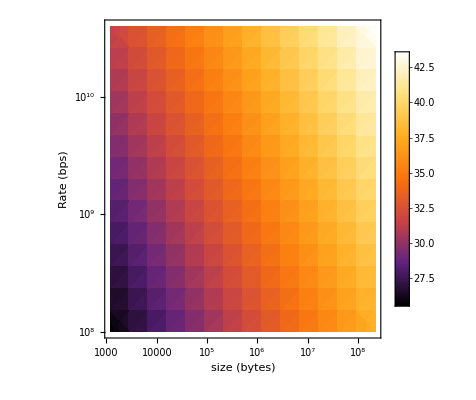

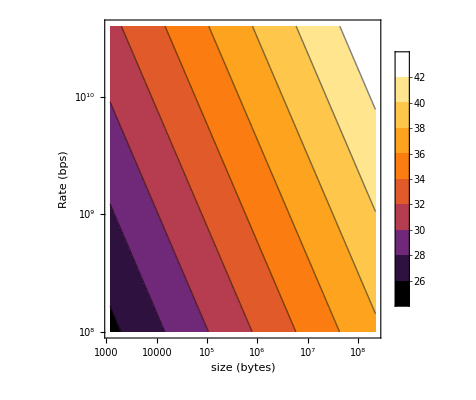

```mathematica
DensityPlot[Log[x r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[x r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

```mathematica
Manipulate[Labeled[Subscript[bb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bb, flowSize][[2]]],Top],{{flowSize,Range[30,42,1][[1]],"insert a flow whose size is greater than"},Range[30,42,1]}]
ListLogLinearPlot[Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
Range[30,42,1][[Position[Map[Last[Subscript[bb, #]]&,Range[30,42,1]],Min[Map[Last[Subscript[bb, #]]&,Range[30,42,1]]]][[1]][[1]]]]
```

-Graphics-

30

Dynamic Threshold Log(Size * Rate):

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-19:10:38-10624".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-19:10:38".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

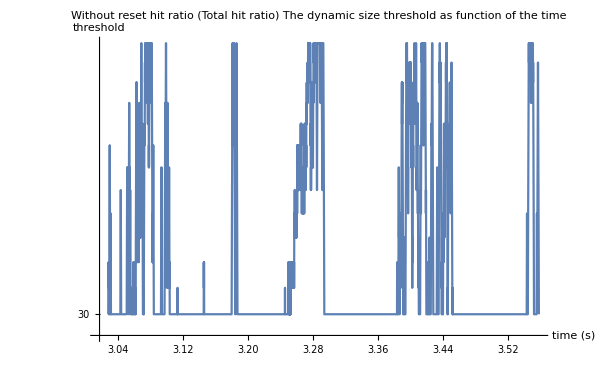

The maximum threshold after 1s is 42
The minimum threshold after 1s is 30

ToExpression::sntx: Invalid syntax in or before "General-0-20221228-19:11:18-12436".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221228-19:11:18".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

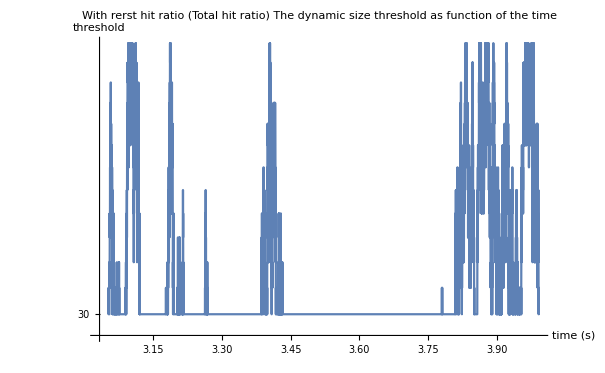

The maximum threshold after 1s is 42
The minimum threshold after 1s is 30

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\3.50000000000000000000  -  4.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\3.50000000000000000000  -  4.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification logreset[[1]] is longer than depth of object.

Part::partd: Part specification logreset[[2]] is longer than depth of object.

Part::partd: Part specification lognonreset[[1]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification logreset⟦1⟧ is longer than depth of object.

Part::partd: Part specification logreset⟦2⟧ is longer than depth of object.

Part::partd: Part specification lognonreset⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
logreset= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\\3.50000000000000000000  -  4.00000000000000000000.txt",True];
lognonreset = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\\3.50000000000000000000  -  4.00000000000000000000.txt",True];
Manipulate[{Labeled[logreset[[1]][[i]],"Threshold learning with reset hit ratio\n Total Avg miss hop = " <> ToString[logreset[[2]]],Top],Labeled[lognonreset[[1]][[i]],"Threshold learning without reset hit ratio\nTotal Avg miss hop = " <> ToString[lognonreset[[2]]],Top]},{{i,1,"flow size index"},1,16,1}]

s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[30,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"},PlotLabel->"Without reset hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]


s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate)dynamic  reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[30,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"},PlotLabel->"With rerst hit ratio (Total hit ratio) \nThe dynamic size threshold as function of the time"]
Print["The maximum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Max,"\nThe minimum threshold after 1s is ",Select[s,#[[1]]≥1&][[All,2]]//Min]
```

Static Ideal Push Algorithm According to size:

```mathematica
Map[(Subscript[c, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 without pull push = "<>ToString[#]<>" flow size\\3.50000000000000000000  -  4.00000000000000000000.txt",False,sizes])&,sizes[[6;;]]];
```

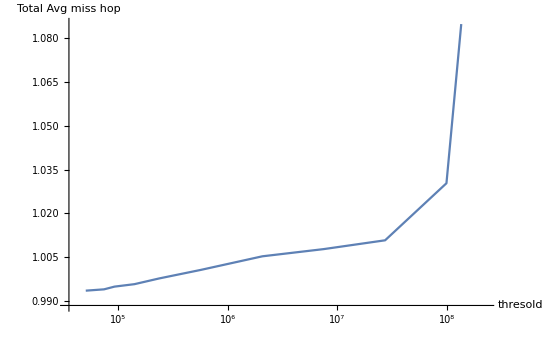

51067

```mathematica
Manipulate[Labeled[Subscript[c, flowSize][[1]],"without pull,insert all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[c, flowSize][[2]]],Top],{{flowSize,sizes[[6]],"insert a flow whose size is greater than"},sizes[[6;;]]}]
ListLogLinearPlot[Map[{#,Subscript[c, #][[2]]}&,sizes[[6;;]]],Joined->True,AxesLabel->{"thresold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[c, #]]&,sizes[[6;;]]],Min[Map[Last[Subscript[c, #]]&,sizes[[6;;]]]]][[1]][[1]]+ 5]]
```

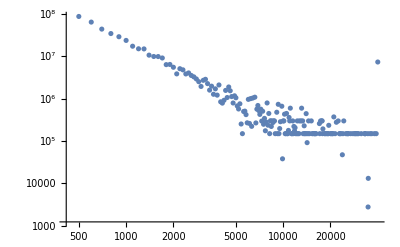

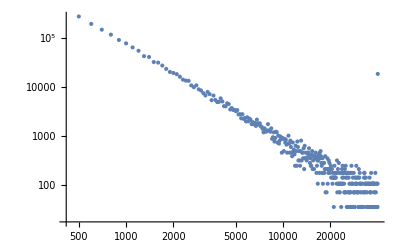

-Graphics-

```mathematica
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==223092956)&]],PlotRange->All]
ListLogLogPlot[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==51067)&]],PlotRange->All]

ListLogLogPlot[Map[Module[{x},x=#;Callout[Map[{#[[2]],#[[3]]}&,Select[data,(#[[1]]==x)&]],x]]&,sizes],PlotRange->All,Joined->True]
```

```mathematica
Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]]
lognonreset[[2]]
logreset[[2]]
```

{{30,True},{31,True},{32,True},{33,True},{34,True},{35,True},{36,True},{37,True},{38,True},{39,True},{40,True},{41,True},{42,True}}

True

True

```mathematica
Row[-Graphics-,-Graphics-]
```

Row[-Graphics-,-Graphics-]

-Graphics-

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf LOG(size Rate) = 39\\3.94999999999999973355  -  4.00000000000000000000.txt",True]
```

plotData[C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\2.5 G with elephant cache = 1000 push = inf LOG(size Rate) = 39\3.94999999999999973355  -  4.00000000000000000000.txt,True]

```mathematica
Range[26,42,1]
```

{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

Static Ideal Elephant Detector According to Size:

```mathematica
Map[(Subscript[bbbb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new static size\\2.5 G cache = 1000 push = inf elephant or pull size greater than "<>ToString[#]<>" final\\4.50000000000000000000  -  5.00000000000000000000.txt",True])&,sizes];
Print[""]
Manipulate[Labeled[Subscript[bbbb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bbbb, flowSize][[2]]],Top],{{flowSize,Range[26,42,1][[1]],"insert a flow whose size is greater than"},sizes}]
ListLogLinearPlot[Map[{#,Subscript[bbbb, #][[2]]}&,sizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
sizes[[Position[Map[Last[Subscript[bbbb, #]]&,sizes],Min[Map[Last[Subscript[bbbb, #]]&,sizes]]][[1]][[1]]]]
```

-Graphics-

1177

Static Ideal Elephant Detector According to Log(Size * Rate):

```mathematica
DensityPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

-Graphics-

-Graphics-

```mathematica
Map[(Subscript[bbb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G cache = 1000 push = inf elephant or pull LOG(size Rate) greater than "<>ToString[#]<>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True])&,Range[26,42,1]];
Print[""]
Manipulate[Labeled[Subscript[bbb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bbb, flowSize][[2]]],Top],{{flowSize,Range[26,42,1][[1]],"insert a flow whose size is greater than"},Range[26,42,1]}]
Row[{ListLogLinearPlot[Map[{#,Subscript[bbb, #][[2]]}&,Range[26,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}],ListLogLinearPlot[Map[{#,Subscript[bbb, #][[2]]}&,Range[26,39,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]}]
Range[26,42,1][[Position[Map[Last[Subscript[bbb, #]]&,Range[26,42,1]],Min[Map[Last[Subscript[bbb, #]]&,Range[26,42,1]]]][[1]][[1]]]]
```

-Graphics--Graphics-

26

Dynamic Elephant Detector According to Hit Ratio (Local/Total):

```mathematica
resetLog =   plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
nonresetLog = plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
resetSize =  plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size with reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];
nonresetSize =  plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size non reset\\4.50000000000000000000  -  5.00000000000000000000.txt",True];

Manipulate[Grid[{{Labeled[resetLog[[1]][[i]],"Threshold log(size * rate)learning with reset hit ratio\n Total Avg miss hop = " <> ToString[resetLog[[2]]],Top],plot1},
{Labeled[nonresetLog[[1]][[i]],"Threshold log(size * rate) learning without reset hit ratio\n Total Avg miss hop = " <> ToString[nonresetLog[[2]]],Top],plot2},
{Labeled[resetSize[[1]][[i]],"Threshold size learning with reset hit ratio\n Total Avg miss hop = " <> ToString[resetSize[[2]]],Top],plot3},
{Labeled[nonresetSize[[1]][[i]],"Threshold size learning without reset hit ratio\n Total Avg miss hop = " <> ToString[nonresetSize[[2]]],Top],plot4}}],{{i,1,"flow size index"},1,16,1}]
```

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

Part::partd: Part specification C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\new dynamic\2.5 G cache = 1000 push = inf dynamic threshold size with reset\4.50000000000000000000  -  5.00000000000000000000.txt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog[[1]] is longer than depth of object.

Part::partd: Part specification resetLog[[2]] is longer than depth of object.

Part::partd: Part specification nonresetLog[[1]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification resetLog⟦1⟧ is longer than depth of object.

Part::partd: Part specification resetLog⟦2⟧ is longer than depth of object.

Part::partd: Part specification nonresetLog⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-20:11:37-15580".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-20:11:37".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

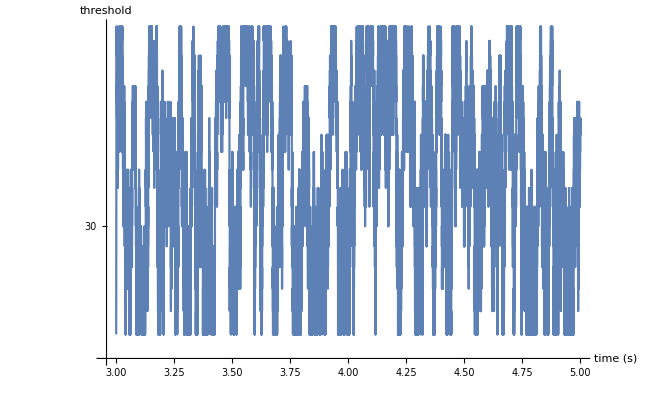

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[25,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot1 = ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-20:11:56-8688".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-20:11:56".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

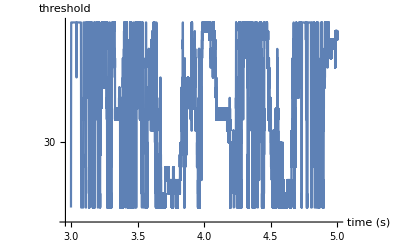

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic log(size rate) threshold size non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[Range[25,42,1],ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot2= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","threshold"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-19:43:28-16708".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-19:43:28".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

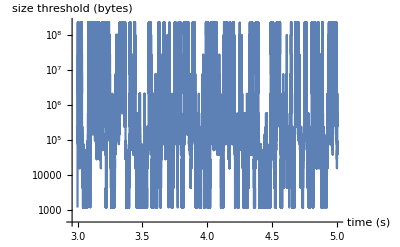

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size with reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot3= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"}]
```

ToExpression::sntx: Invalid syntax in or before "General-0-20221231-19:43:54-13840".
                                                                       ^

ToExpression::sntx: Invalid syntax in or before "20221231-19:43:54".
                                                             ^

ToExpression::sntxi: Incomplete expression; more input is needed .

ToExpression::sntx: Invalid syntax in or before "reset/\""".
                                                       ^

General::stop: Further output of ToExpression::sntx will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

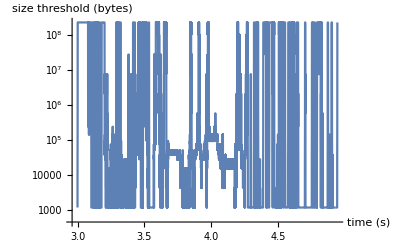

```mathematica
s=Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new dynamic\\2.5 G cache = 1000 push = inf dynamic threshold size non reset\\General-#0.vec","List"];
s=Select[s,MemberQ[sizes,ToExpression[Last[StringSplit[#]]]]&];
s=Select[s,StringSplit[#][[1]]=="0"&];
s=Map[{ToExpression[StringSplit[#][[3]]],ToExpression[StringSplit[#][[4]]]}&,s];
plot4= ListLogPlot[s,Joined->True,AxesLabel->{"time (s)","size threshold (bytes)"}]
```

```mathematica
Grid
```

Grid

```mathematica
resetLog===nonresetLog
```

False

```mathematica
Range[26,42,1]
```

{26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42}

```mathematica
Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]]
```

{1177,1691.5,2206,2720.5,3235,3749.5,4264,6127.17,7990.33,9853.5,11716.7,13579.8,15443,17535.8,19628.7,21721.5,23814.3,25907.2,28000,29553.8,31107.7,32661.5,34215.3,35769.2,37323,39613.7,41904.3,44195,46485.7,48776.3,51067,55040.5,59014,62987.5,66961,70934.5,74908,77972.2,81036.3,84100.5,87164.7,90228.8,93293,101381.,109468.,117556,125644.,133731.,141819,157825.,173830.,189836,205842.,221847.,237853,293768.,349683.,405599.,461514.,517429.,573344,823911.,1070000,1330000,1580000,1830000,2076744,2980000,3890000,4800000,5710000,6610000,7521945,10800000,14100000,17400000,20700000,24000000,27244995,39200000,51100000,63000000,74900000,86800000,98686787,119000000,140000000,161000000,182000000,202000000,223092956}

Static Ideal Elephant Detector According to Log(Size * Rate):

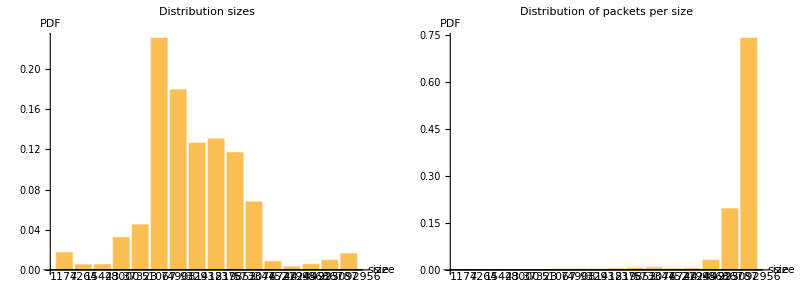

```mathematica
Subscript[a, 1] = BarChart[distOfSizes,ChartLabels->sizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];
Subscript[a, 2]=BarChart[Table[N[(distOfSizes[[j]]*sizes[[j]])/Total[Table[distOfSizes[[i]]*sizes[[i]],{i,1,16}]]],{j,1,16}],ChartLabels->sizes,PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Grid[{{Subscript[a, 1],Subscript[a, 2]}}]
```

Static Ideal Elephant Detector According to Log(Size * Rate):

DensityPlot::exclul: {Im[ⅇ^(Charting`Private`pvar$51496) result$51504]-0} must be a list of equalities or real-valued functions.

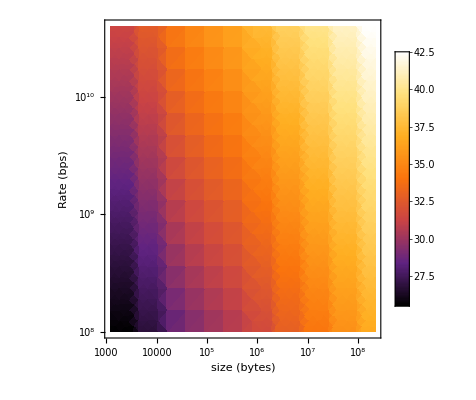

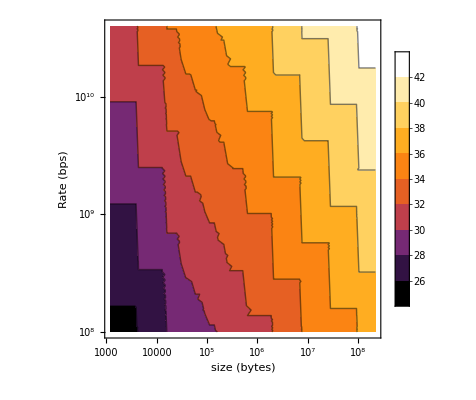

```mathematica
f[x_]:=Module[{result},Table[If[x ≤ sizes[[i]] && x ≥ sizes[[i-1]],result = sizes[[i-1]] ],{i,2,Length[sizes]}];result];
DensityPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
ContourPlot[Log[f[x] r],{x,Min[sizes],Max[sizes]},{r,100 10^6,40 10^9},ScalingFunctions->{"Log","Log"},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"size (bytes)","Rate (bps)","Log(size * rate)"}]
```

```mathematica
Map[(Subscript[bb, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 log pull = "<>ToString[#]<>", push = inf,inf\\3.50000000000000000000  -  4.00000000000000000000.txt",True])&,Range[30,42,1]];
Manipulate[Labeled[Subscript[bb, flowSize][[1]],"push = ∞,∞  pull all sizes >= " <> ToString[flowSize] <> "\nTotal Avg miss hop = " <> ToString[Subscript[bb, flowSize][[2]]],Top],{{flowSize,Range[30,42,1][[1]],"insert a flow whose size is greater than"},Range[30,42,1]}]
ListLogLinearPlot[Map[{#,Subscript[bb, #][[2]]}&,Range[30,42,1]],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"}]
Range[30,42,1][[Position[Map[Last[Subscript[bb, #]]&,Range[30,42,1]],Min[Map[Last[Subscript[bb, #]]&,Range[30,42,1]]]][[1]][[1]]]]
```

-Graphics-

30

BarChart::ldata: True/Total[True] is not a valid dataset or list of datasets.

General::stop: Further output of BarChart::ldata will be suppressed during this calculation.

BarChart[True/Total[True],ChartLabels→True,PlotLabel→Distribution of sizes in the simulation,AxesLabel→{size,PDF}]

Part::partd: Part specification Null⟦1⟧ is longer than depth of object.

BarChart[True/Total[True],ChartLabels→True,PlotLabel→Distribution of sizes in the simulation,AxesLabel→{size,PDF}]

Part::partd: Part specification Null⟦2⟧ is longer than depth of object.

The new distribution of the sizes:

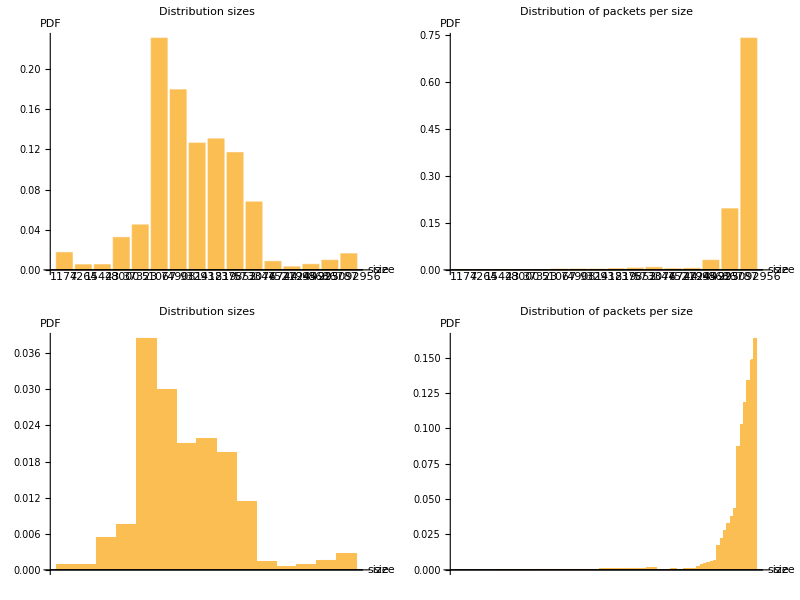

```mathematica
newdistOfSizes = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\size_distribution\\i-hadoop.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
Subscript[a, 3]:=BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}];

Subscript[a, 4]:=BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}];
Total[Table[sizes[[i]]*distOfSizes[[i]],{i,1,Length[sizes]}]];
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]];

Grid[{{Subscript[a, 1],Subscript[a, 2]},{Subscript[a, 3],Subscript[a, 4]}}]
```

```mathematica
Map[(Subscript[b, #]= plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\2.5 G with elephant cache = 1000 push = inf  pull great then " <> ToString[#] <>"\\4.50000000000000000000  -  5.00000000000000000000.txt",True,sizes])&,sizes];
```

```mathematica
plotData["C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with quantile cache=1000\2.5 G cache=1000 push in cont_swt=117556,push in agg_swt=117556\13.00000000000000000000-14.00000000000000000000.txt",True,sizes]
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with quantile cache=1000\2.5 G cache=1000 push in cont_swt=117556,push in agg_swt=117556\13.00000000000000000000-14.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72302&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$72302& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$72302& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72302&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$72391&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

{{-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.,-Graphics-Avg miss hop = 1.},1.}

####################################################################################################################################################

```mathematica
ff[cnt_,agg_,chooseSize_]:=(
str = Import["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with quantile cache = 1000\\2.5 G cache = 1000 push in cont_swt = "<>ToString[cnt]<>",push in agg_swt = "<>ToString[agg]<>"\\13.00000000000000000000  -  14.00000000000000000000.txt"];
listStrings = StringSplit[str,{"#######################################################\nmiss_count_map:{size,rate,count,value}\n","#######################################################\nout of order:{size,rate,count,value}\n"}];
missCount = ToExpression[ StringDrop[listStrings[[1]],{-4}]];
sum = Total[Map[#[[3]]&,missCount]];
data = Map[{#[[1]],100*#[[2]],#[[3]]}&,missCount];

(*The miss count:*)
missCountList= Map[{#[[1]],100*#[[2]],(#[[4]])/(#[[3]])}&,missCount];
If[True == True,rtt = (5.8)*10^-6,pivot =9.2*10^-6];
pivot = (1500*8)/rtt;
return = Module[{s,oneSzie,oneSum,oneMean},s=Floor[chooseSize];
oneSzie = Select[missCount,(#[[1]]==s)&];
oneSum = Total[Map[#[[3]]&,oneSzie]];
oneMean = N[Total[Map[#[[4]]&,oneSzie]]/oneSum];
Labeled[ListLogLinearPlot[Map[{#[[2]],#[[3]]}&,Select[missCountList,(#[[1]]==s)&]],PlotRange->{Automatic,{0.,3}},PlotLabel->"size =  " <> ToString[s] <> "\n#packets = " <> ToString[N[s/1500]],AxesLabel->{"Rate (Mbps)","Avg miss hop"},Epilog->{Red,Line[Table[{Log[pivot/10^6],i},{i,0,3,0.01}]],Text[Style["rate corresponds to RTT\nrate = " <> ToString[pivot/10^6] <> " Mbps",Tiny],Automatic]}],"Avg miss hop = " <> ToString[oneMean]]
];
Return[{return,N[Total[Map[#[[4]]&,missCount]]/sum]}]);
```

```mathematica
117556
```

117556

```mathematica
ff[117556,117556,1070000]
ff[117556,117556,90228.8]
```

{-Graphics-Avg miss hop = 0.973705,0.93399}

{-Graphics-Avg miss hop = 2.51826,0.93399}

```mathematica
quantiles = {37323,44195,51067,62987.5,74908,90228.8,117556,173830,293768,223092956};
```

```mathematica
Map[{#,ff[#,#,1070000][[2]]}&,quantiles]
```

{{37323,0.935804},{44195,0.94063},{51067,0.939488},{62987.5,0.949062},{74908,0.9342},{90228.8,0.94843},{117556,0.93399},{173830,0.955235},{293768,0.938795},{223092956,2.21813}}

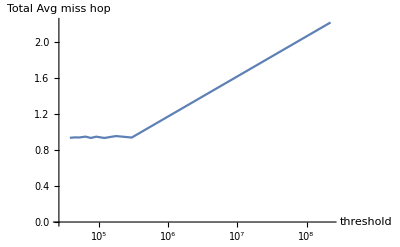

```mathematica
ListLogLinearPlot[Map[{#,ff[#,#,1070000][[2]]}&,quantiles],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

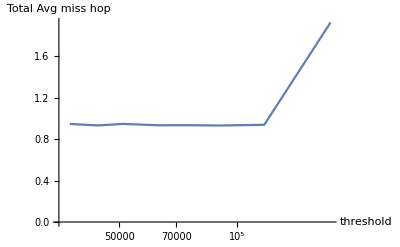

```mathematica
ListLogLinearPlot[Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

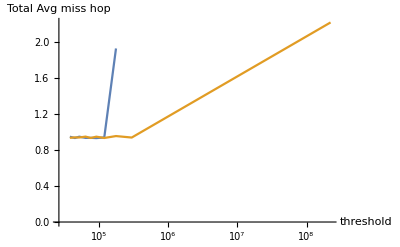
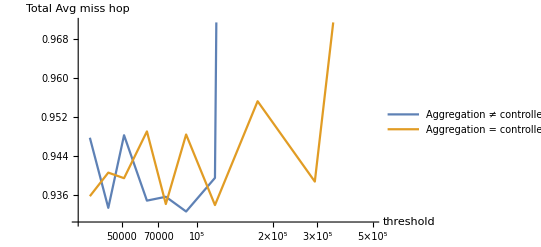
-Graphics- | -Graphics-

```mathematica
aaa = ListLogLinearPlot[{Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Map[{#,ff[#,#,1070000][[2]]}&,quantiles]},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All];
bbb = ListLogLinearPlot[{Table[{quantiles[[i]],ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]]},{i,1,Length[quantiles]-2}],Map[{#,ff[#,#,1070000][[2]]}&,quantiles]},PlotLegends->{"Aggregation ≠ controllerswitch","Aggregation = controllerswitch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{{0,500000},Automatic}];
Grid[{{aaa,bbb}}]
```

```mathematica
Table[ff[quantiles[[i]],quantiles[[i+2]],1070000][[2]],{i,1,Length[quantiles]-2}]
```

{0.947765,0.933417,0.948281,0.934899,0.935688,0.932673,0.939548,1.92883}

```mathematica
Manipulate[Quiet[Module[{x},x=ff[cnt,agg,chooseSize];Grid[{{x[[1]],"Total Avg miss count = "<> ToString[x[[2]]]}}]]],{{cnt,quantiles[[1]],"The threshold in the controller switch"},quantiles},{{agg,quantiles[[1]],"The threshold in the aggregation switch"},quantiles},{{chooseSize,newsizes[[1]],"The size we observe"},newsizes}]
```

The new distribution of the sizes:

-Graphics-

```mathematica
Manipulate[Quiet[Module[{x},x=ff[cnt,agg,chooseSize];Grid[{{x[[1]],"Total Avg miss count = "<> ToString[x[[2]]]}}]]],{{cnt,quantiles[[1]],"The threshold in the controller switch"},quantiles},{{agg,quantiles[[1]],"The threshold in the aggregation switch"},quantiles},{{chooseSize,newsizes[[1]],"The size we observe"},newsizes}]
```

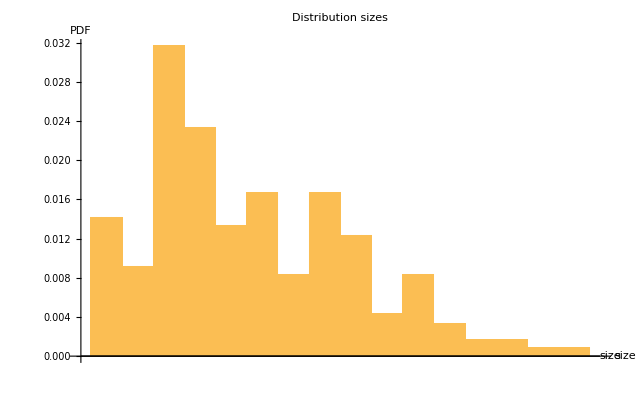

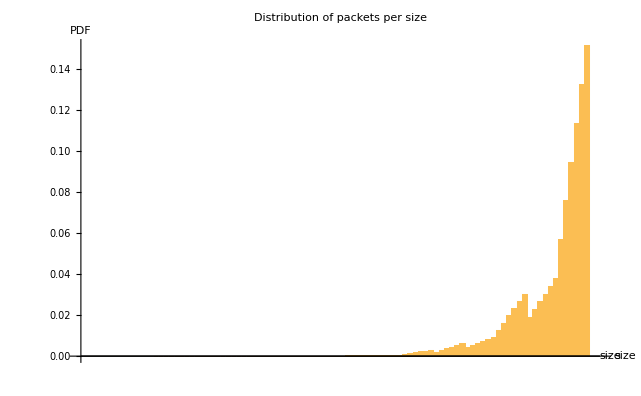

5.50755×10^6

```mathematica
newdistOfSizes = Import["C:\\Users\\0wner\\Downloads\\i-datamining.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\Users\\0wner\\Downloads\\i-datamining.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]

BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]]
```

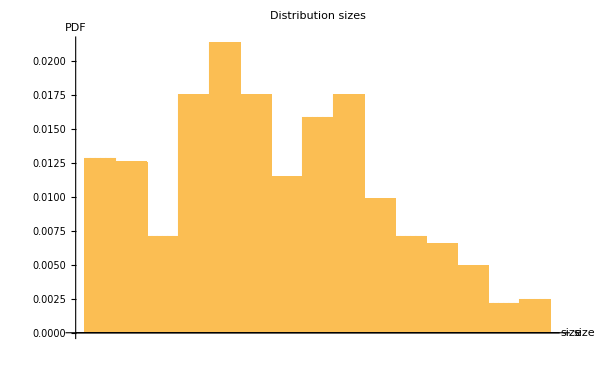

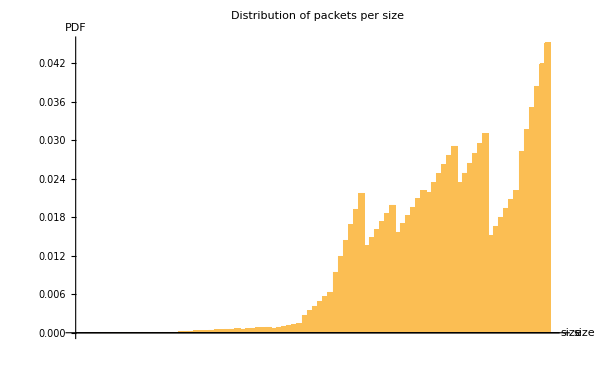

4.866×10^6

1.55469×10^6

```mathematica
newdistOfSizes = Import["C:\\Users\\0wner\\Downloads\\i-websearch.csv","Grid"][[1]][[2;;]][[All,2]];
newdistOfSizes=Table[newdistOfSizes[[i]] - newdistOfSizes[[i-1]],{i,2,Length[newdistOfSizes]}];
newsizes = Import["C:\\Users\\0wner\\Downloads\\i-websearch.csv","Grid"][[1]][[2;;]][[All,1]][[2;;]];
BarChart[newdistOfSizes,PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]

BarChart[Table[N[(newdistOfSizes[[j]]*newsizes[[j]])/Total[Table[newdistOfSizes[[i]]*newsizes[[i]],{i,1,Length[newsizes]}]]],{j,1,Length[newsizes]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
Total[Table[sizes[[i]]*distOfSizes[[i]],{i,1,Length[sizes]}]]
Total[Table[newsizes[[i]]*newdistOfSizes[[i]],{i,1,Length[newsizes]}]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

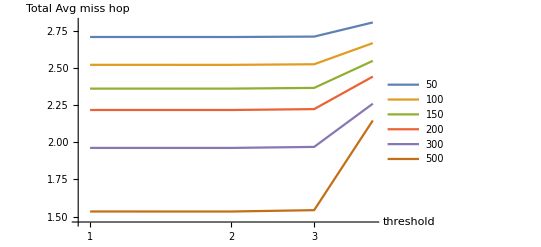

```mathematica
ListLogLinearPlot[Map[Module[{x},x=#;Map[plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[x]<>" push in cont_swt,agg_swt = "<>ToString[#]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]&,{1177,28000,27244995,223092956}]]&,{50,100,150,200,300,500}],PlotLegends->{50,100,150,200,300,500},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

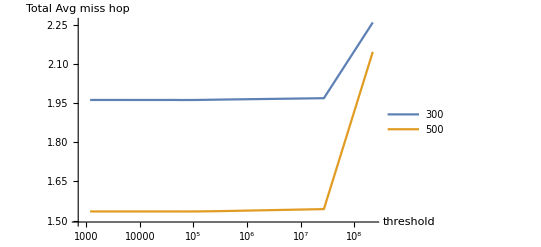

```mathematica
ListLogLinearPlot[Map[Module[{x},x=#;Map[{#,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[x]<>" push in cont_swt,agg_swt = "<>ToString[#]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{1177,28000,37323,51067,62987.5,74908,90228.8,117556,293768,27244995,223092956}]]&,{300,500}],PlotLegends->{300,500},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

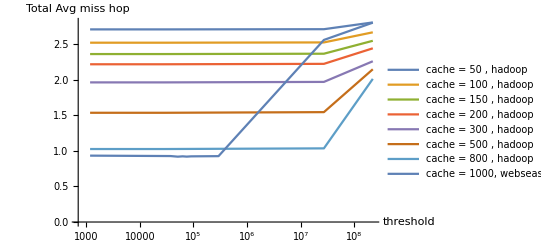

| 1177 | 28000 | 27244995 | 223092956
50 | 2.70663 | 2.70643 | 2.70922 | 2.8043
100 | 2.5196 | 2.51949 | 2.52347 | 2.66551
150 | 2.36002 | 2.36001 | 2.36475 | 2.54642
200 | 2.21643 | 2.21646 | 2.22231 | 2.44065
300 | 1.96187 | 1.96182 | 1.96862 | 2.25874
500 | 1.5349 | 1.53484 | 1.54386 | 2.14616
800 | 1.02559 | 1.02549 | 1.03478 | 2.01111

```mathematica
x=Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{50,100,150,200,300,500,800},{1177,28000,27244995,223092956}];
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,37323,51067,62987.5,74908,90228.8,117556,293768,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

```mathematica
{{"", 1177, 28000, 27244995, 223092956}, {50, 2.7066305282255563, 2.7064303666126994, 2.7092191268121826, 2.8043034923533683}, {100, 2.5196015565490786, 2.519487487786739, 2.523466170767454, 2.665510283363781}, {150, 2.3600185841333823, 2.3600139744590796, 2.3647508500004224, 2.5464178464436173}, {200, 2.2164271494775885, 2.216457922772359, 2.2223106338710323, 2.4406491094435}, {300, 1.961869639209376, 1.9618204029848043, 1.9686245016508455, 2.258738331986653}, {500, 1.5349034781249793, 1.534840644511449, 1.5438629958351842, 2.146162895955437}, {800, 1.0255888887383415, 1.0254861415554506, 1.0347786757586377, 2.011109921346558}}
```

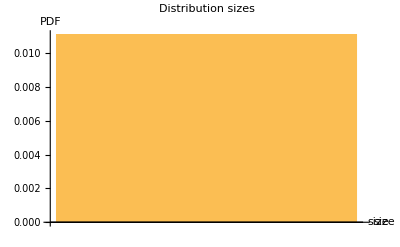

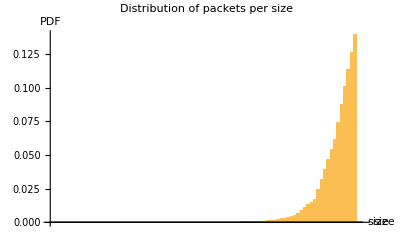

```mathematica
BarChart[ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length],PlotLabel->"Distribution sizes",AxesLabel->{"size","PDF"}]
BarChart[Table[N[(ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length][[j]]*sizesHadoop[[j]] )/Total[Table[ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length][[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
```

```mathematica
(*{1177,28000,37323,51067,62987.5,117556,27244995,223092956}*)
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with different cache sizes i websearch\2.5 G cache = 1000 push in cont_swt,agg_swt = 28000\10.50000000000000000000  -  11.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$2241847& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$2241847& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241934&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

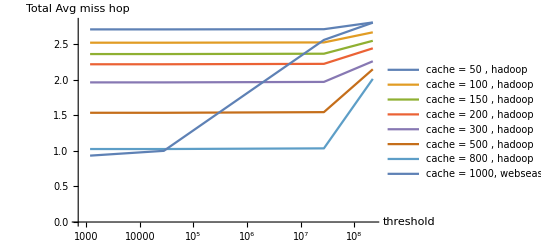

Transpose::nmtx: The first two levels of {{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},«4»,{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Grid[Transpose[Join[{{,50,100,150,200,300,500,800}},Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},{2.5196,2.51949,2.52347,2.66551},{2.36002,2.36001,2.36475,2.54642},{2.21643,2.21646,2.22231,2.44065},{1.96187,1.96182,1.96862,2.25874},{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}}]]],Frame→All,Background→{{1→RGBColor[1, 1, 0]},{1→RGBColor[1, 1, 0]}}]

```mathematica
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,28000,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

```mathematica
x=Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i hadoop\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.00000000000000000000  -  10.50000000000000000000.txt",True,newsizes][[2]]}&,{50,100,150,200,300,500,800},{1177,28000,27244995,223092956}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
x
```

{{{1177,2.70663},{28000,2.70643},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.70922},{223092956,2.8043}},{{1177,2.5196},{28000,2.51949},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.52347},{223092956,2.66551}},{{1177,2.36002},{28000,2.36001},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.36475},{223092956,2.54642}},{{1177,2.21643},{28000,2.21646},{37323,1.},{51067,1.},{62987.5,1.},{117556,1.},{27244995,2.22231},{223092956,2.44065}},{{1177,1.96187},{28000,1.96182},{37323,1.96192},{51067,1.96174},{62987.5,1.96156},{117556,1.96188},{27244995,1.96862},{223092956,2.25874}},{{1177,1.5349},{28000,1.53484},{37323,1.53478},{51067,1.53492},{62987.5,1.53467},{117556,1.53497},{27244995,1.54386},{223092956,2.14616}},{{1177,1.02559},{28000,1.02549},{37323,1.0252},{51067,1.02502},{62987.5,1.02481},{117556,1.02525},{27244995,1.03478},{223092956,2.01111}}}

```mathematica
Apply[Join,Apply[Join,Outer[{#1,#2,#3}&,{1,2},{3,4},{5,6,7}]]]
```

{{1,3,5},{1,3,6},{1,3,7},{1,4,5},{1,4,6},{1,4,7},{2,3,5},{2,3,6},{2,3,7},{2,4,5},{2,4,6},{2,4,7}}

```mathematica
sizesDataMining//Length
sizesHadoop//Length
sizesWebSearch//Length
ConstantArray[1/(sizesHadoop//Length),sizesHadoop//Length]
```

96

90

90

{1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90,1/90}

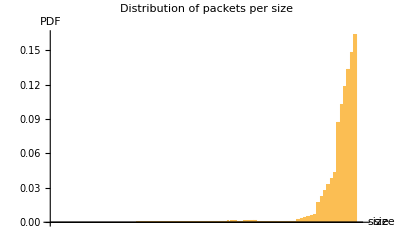

```mathematica
BarChart[Table[N[(distOfSizesHadoop[[j]]*sizesHadoop[[j]])/Total[Table[distOfSizesHadoop[[i]]*sizesHadoop[[i]],{i,1,Length[sizesHadoop]}]]],{j,1,Length[sizesHadoop]}],PlotLabel->"Distribution of packets per size",AxesLabel->{"size","PDF"}]
```

```mathematica
(Select[RandomInteger[100,10000000],(#==100)&]//Length)/10000000//N
```

0.0099234

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 150000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 15000000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.38484

2.20937

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 150000\\7.00000000000000000000  -  7.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test t = 15000000\\7.00000000000000000000  -  7.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.38491

2.20917

```mathematica
97121912 - 9510344
```

87611568

```mathematica
2.3848407478945837/2.2093706513635594
```

1.07942

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 1 t = 150000\\5.50000000000000000000  -  6.00000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 1 t = 15000000\\5.50000000000000000000  -  6.00000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

3.

3.

```mathematica
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 2 t = 150000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test c = 2 t = 15000000\\5.00000000000000000000  -  5.50000000000000000000.txt",False,{150000 ,15000000}][[2]]
```

2.59824

2.40818

```mathematica
StringLength["my_results/The new results/"]
```

27

```mathematica
StringDelete[StringRiffle[ConstantArray["a",27]]," "]
```

aaaaaaaaaaaaaaaaaaaaaaaaaaa

```mathematica
1600000000000/10^12//N
```

1.6

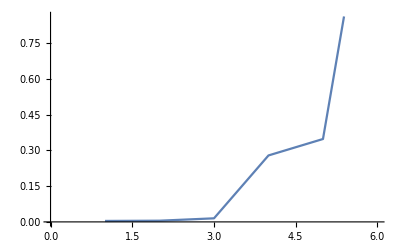

```mathematica
ListPlot[{0.004,0.005,0.01499,0.279,0.348,1.68},Joined->True]
```

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"50% of the traffic is App A and 50% is App B",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

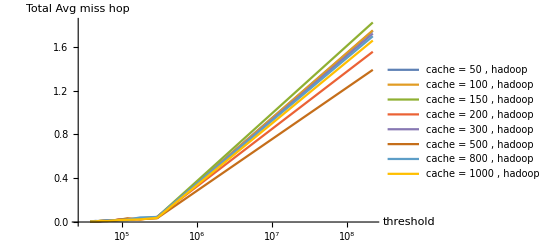

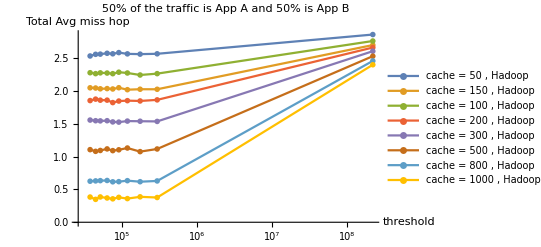

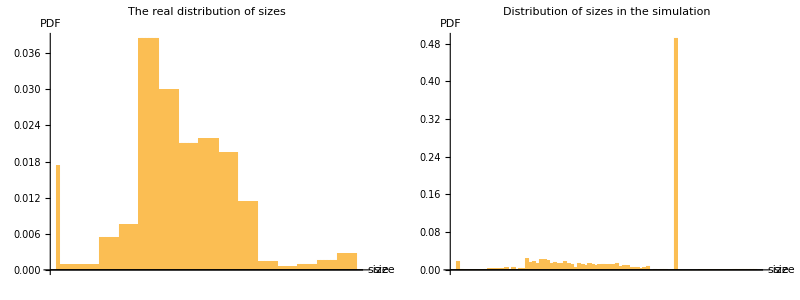

```mathematica
plotgraph[2.5,1.6 *10^12,{50,100,150,200,300,500,800,1000},{37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956},"hadoop"]
```

```mathematica
Show[
ListLogLinearPlot[x,PlotLegends->Map["cache = "<>ToString[#]<>" , hadoop"&,{50,100,150,200,300,500,800}],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All],
ListLogLinearPlot[Outer[{#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\static push with different cache sizes i websearch\\2.5 G cache = "<>ToString[#1]<>" push in cont_swt,agg_swt = "<>ToString[#2]<>"\\10.50000000000000000000  -  11.00000000000000000000.txt",True,sizesWebSearch][[2]]}&,{1000},{1177,28000,27244995,223092956}],PlotLegends->{"cache  = 1000, webseasrch"},Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->All]]
Grid[Transpose[{{"",50,100,150,200,300,500,800}}~Join~Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956}}~Join~x[[All,All,2]]]],Frame->All,Background->{{1->Yellow},{1->Yellow}}]
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results\static push with different cache sizes i websearch\2.5 G cache = 1000 push in cont_swt,agg_swt = 28000\10.50000000000000000000  -  11.00000000000000000000.txt not found during Import.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,{#######################################################
miss_count_map:{size,rate,count,value}
,#######################################################
out of order:{size,rate,count,value}
}].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[$Failed,{-4}].

ToExpression::notstrbox: StringDrop[$Failed,{-4}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of (_map:{size,rate,count,valu}) miss_count does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partw: Part 3 of #1⟦1⟧==s$2241847& does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification $Failed⟦4⟧ is longer than depth of object.

Part::partw: Part 4 of #1⟦1⟧==s$2241847& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241847&].

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦1⟧==s$2241934&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

-Graphics-

Transpose::nmtx: The first two levels of {{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},«4»,{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}} cannot be transposed.

Join::heads: Heads List and Transpose at positions 1 and 2 are expected to be the same.

Grid[Transpose[Join[{{,50,100,150,200,300,500,800}},Transpose[{{1177,28000,37323,51067,62987.5,117556,27244995,223092956},{2.70663,2.70643,2.70922,2.8043},{2.5196,2.51949,2.52347,2.66551},{2.36002,2.36001,2.36475,2.54642},{2.21643,2.21646,2.22231,2.44065},{1.96187,1.96182,1.96862,2.25874},{1.5349,1.53484,1.54386,2.14616},{1.02559,1.02549,1.03478,2.01111}}]]],Frame→All,Background→{{1→RGBColor[1, 1, 0]},{1→RGBColor[1, 1, 0]}}]

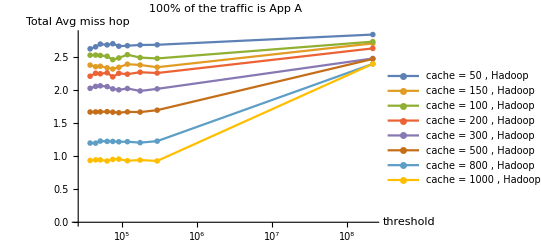

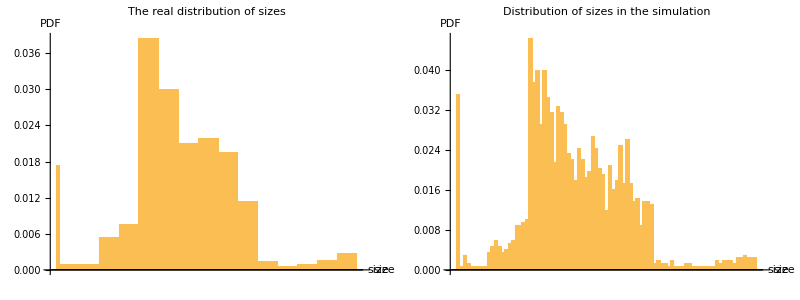

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results with old hosts\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"100% of the traffic is App A",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results with old hosts\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {50,150, 100,200,300,500,800,1000};
thresholds = {37323,44195,51067,62987.5,74908,90228.8,117556,173830.,293768.,223092956};
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"50% of the traffic is App A and 50% is App B",PlotMarkers->"OpenMarkers"]
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results\\end time = 3.006s rate = 2.5G size distribution = i-hadoop cache size = 300 push threasholds = 117556\\Total.txt",sizesHadoop]
```

-Graphics-

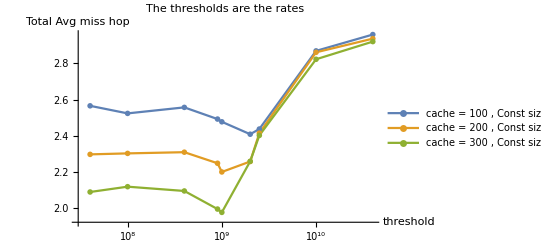

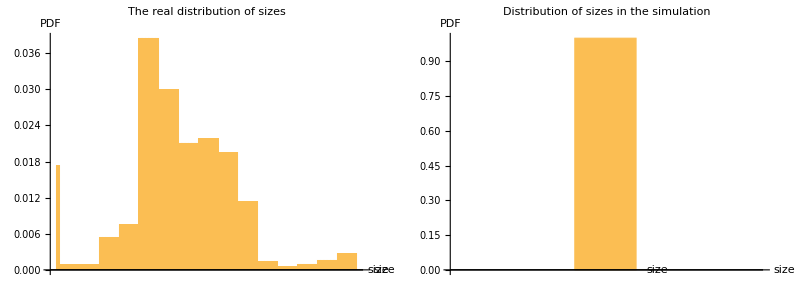

```mathematica
sizeDistribution = "Const size = 4M B";
cacheSizes = {100,200,300};
thresholds = Sort[{2500000000,40000000000,40000000,400000000,100000000,900000000,1000000000,2000000000,10000000000}];
ListLogLinearPlot[Tooltip[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\ccc rate\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds]],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\ccc rate\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 300 push threasholds = 2500000000\\Total.txt",sizesHadoop]
```

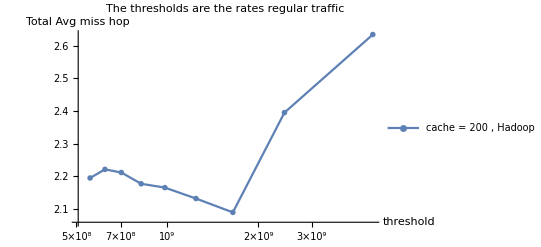

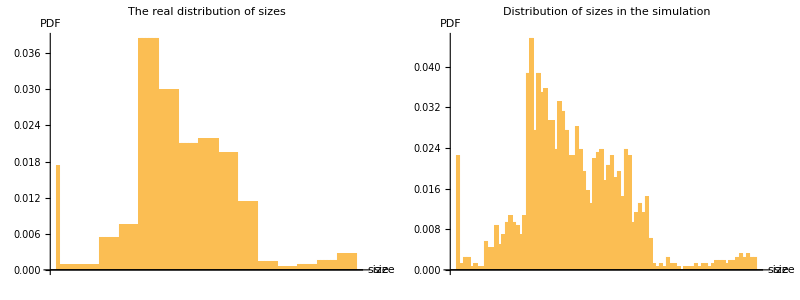

```mathematica
sizeDistribution = "Hadoop";
cacheSizes = {200};
thresholds = Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates regular traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 200 push threasholds = 621504292\\Total.txt",sizesHadoop]
```

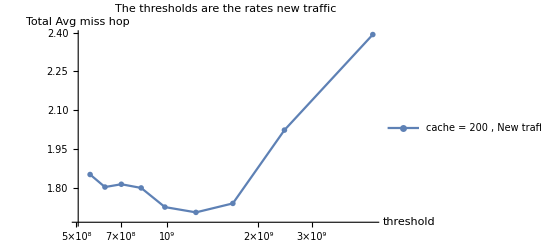

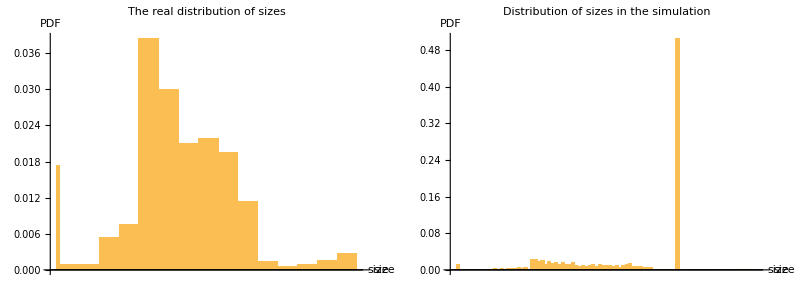

```mathematica
sizeDistribution = "New traffic";
cacheSizes = {200};
thresholds = Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate new hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate new hosts\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = 200 push threasholds = 621504292\\Total.txt",sizesHadoop]
```

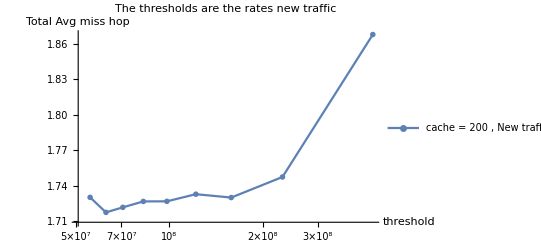

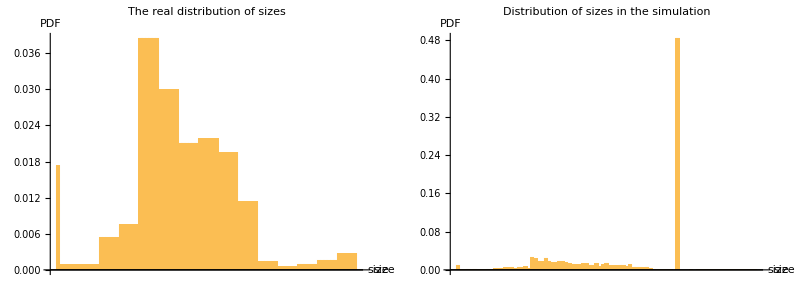

```mathematica
sizeDistribution = "New traffic";
cacheSizes = {200};
thresholds = Sort[{55658062,62593416,70927071,82556950,98284489,121805866,158245781,231309663,451566338}];
ListLogLinearPlot[Outer[(temp={#2,plotData["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 15.006s rate = 400M const size distribution = i-hadoop cache size = "<>ToString[#1]<>" push threasholds = "<>ToString[#2]<>"\\Total.txt",True,sizesHadoop][[2]]};Tooltip[temp,temp])&,cacheSizes,thresholds],PlotLegends->Map["cache = "<>ToString[#]<>" , "<>sizeDistribution&,cacheSizes],Joined->True,AxesLabel->{"threshold","Total Avg miss hop"},PlotRange->{All,All},PlotLabel->"The thresholds are the rates new traffic",PlotMarkers->"OpenMarkers"]//Quiet
sizeDistributionValidationI["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new results rate old hosts\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = 200 push threasholds = 70927071\\Total.txt",sizesHadoop]
```

Types of applications:

```mathematica
{{"Type", "Description of the Application"}, {"Application A", "The sizes of app A are drawn from i-Hadoop distribution and the destination is drawn from a large Range"}, {"Application B(x)", "The sizes of app B(x) are constant and equal to x and the destination is drawn from a small Range"}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}}
```

Type | Description of the Application
Application A | The sizes of app A are drawn from i-Hadoop distribution and the destination is drawn from a large Range
Application B(x) | The sizes of app B(x) are constant and equal to x and the destination is drawn from a small Range
 | 
 | 
 | 
 | 
 | 
 | 
 |

Types of traffic:

```mathematica
{{"Type", "Description of the traffic"}, {"Traffic A", "All flows is from App A"}, {"Traffic B", "The flows are from app A with a probability of 1/2 and from app B(Avg(Hadoop)) with a probability of 1/2"}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}, {"", ""}}
```

Type | Description of the traffic
Traffic A | All flows is from App A
Traffic B | The flows are from app A with a probability of 1/2 and from app B(Avg(Hadoop)) with a probability of 1/2
 | 
 | 
 | 
 | 
 | 
 | 
 |

Benchmark: Push Fast Cache on Traffic B

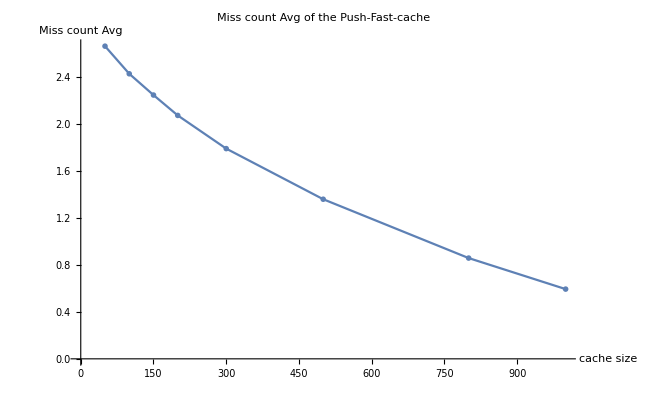

```mathematica
pushFastCacheList = Map[{#,missCountAvg[StringReplace["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{"AAA"->ToString[#],"BBB"->ToString[0]}]]}&,{50,100,150,200,300,500,800,1000}];
ListPlot[Map[Tooltip[#,#]&,pushFastCacheList],Joined->True,PlotMarkers->"OpenMarkers",PlotLabel->"Miss count Avg of the Push-Fast-cache",AxesLabel->{"cache size","Miss count Avg"}]
```

Rates: 2.5G Avg      Traffic: Traffic B

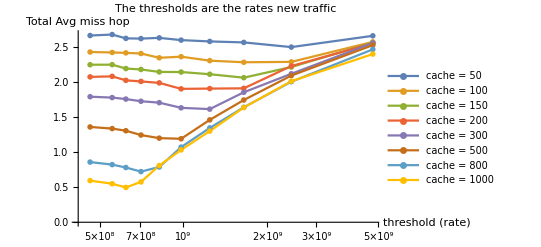

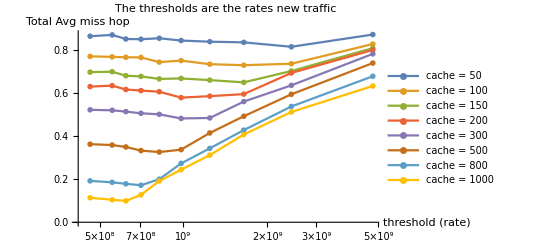

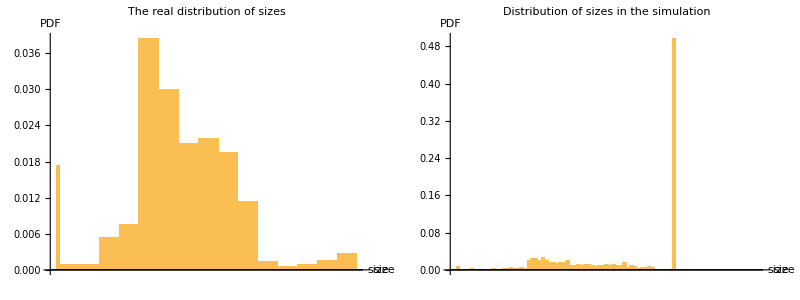

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
50 | 6.19965 | 2437615808 | 5.68238 | 2437615808
100 | 6.01866 | 1645830947 | 5.32464 | 1645830947
150 | 8.22908 | 1645830947 | 6.81979 | 1645830947
200 | 8.23435 | 980967951 | 8.12497 | 980967951
300 | 9.88298 | 1242635857 | 7.6955 | 980967951
500 | 12.4222 | 980967951 | 10.0647 | 818901538
800 | 15.8301 | 704099360 | 10.563 | 704099360
1000 | 16.3723 | 621504292 | 12.8914 | 621504292

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

```mathematica
1500*8*70/((1500*8*10)/555037325)
```

3885261275

Rate Estimator 1: (port-destination) Rate estimator in each switch Rates: 2.5G Avg      Traffic: Traffic B

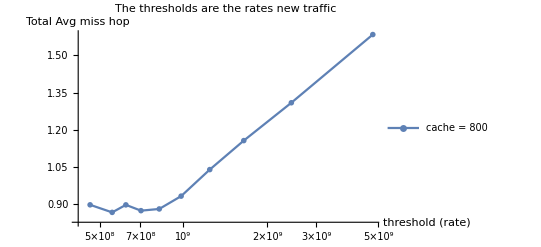

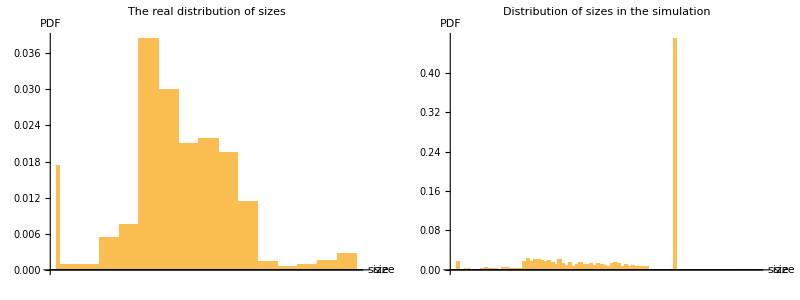

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
800 | 3.41446 | 4.80506

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\port-dest-esti\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rate Estimator 2: Rate estimator only by destination in each switch Rates: 2.5G Avg      Traffic: Traffic B

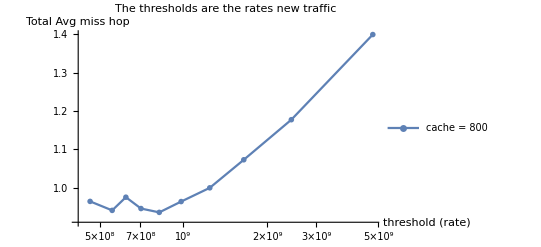

-Graphics-

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
800 | 2.97098 | 3.16667

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\total-rate-esti\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic A

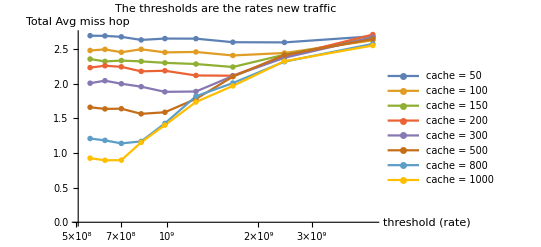

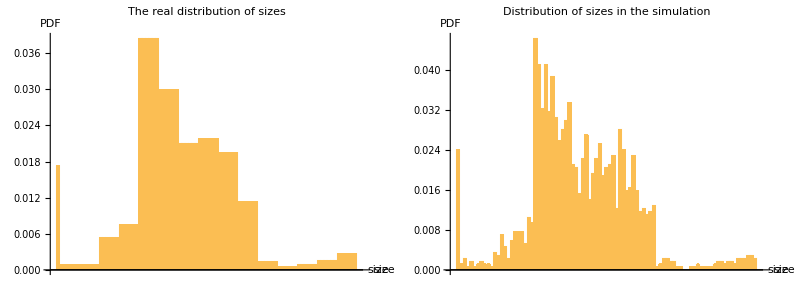

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 3.60356 | 3.39992
100 | 2.89994 | 2.41642
150 | 4.87205 | 3.84225
200 | 5.24578 | 4.14327
300 | 6.22426 | 5.20619
500 | 5.71595 | 3.76141
800 | 5.83444 | 1.85578
1000 | 3.2763 | 1.11022×10^-14

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\regular traffic\\end time = 3.006s rate = 2.5G const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 400M Avg      Traffic: Traffic B

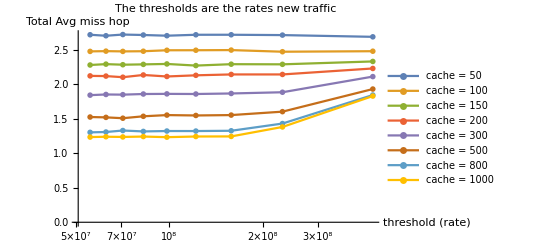

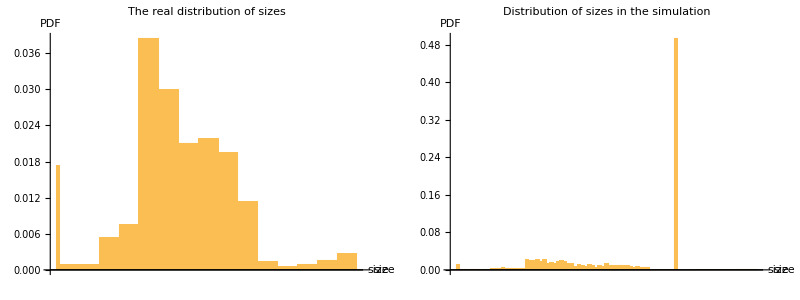

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 1.10356 | 0.829167
100 | 0.198403 | 1.11022×10^-14
150 | 0.368824 | 0.417844
200 | 0.908985 | 1.20741
300 | 0. | 0.
500 | 1.12836 | 1.79312
800 | 0. | 1.42561
1000 | 0.107216 | 1.73593

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\new traffic 400M\\end time = 20.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{55658062,62593416,70927071,82556950,98284489,121805866,158245781,231309663,451566338}]]
```

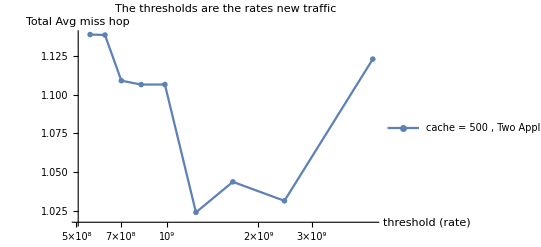

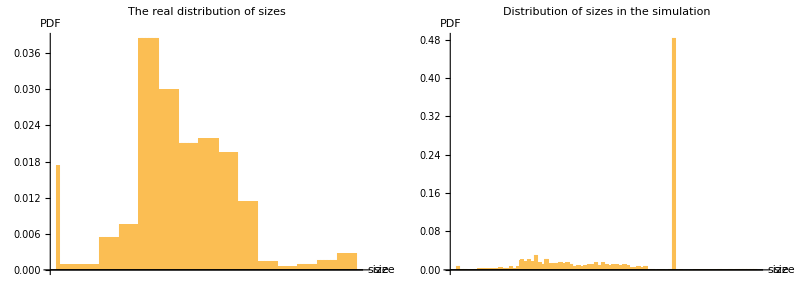

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
500 | 10.0892 | 7.339

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B hadoop\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B  Estimate Rate Window: 10 μs

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

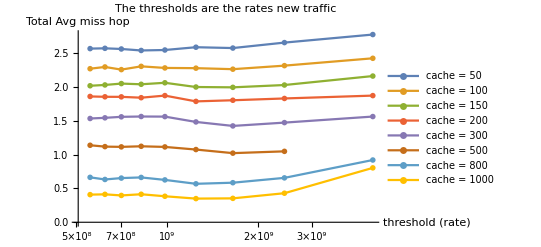

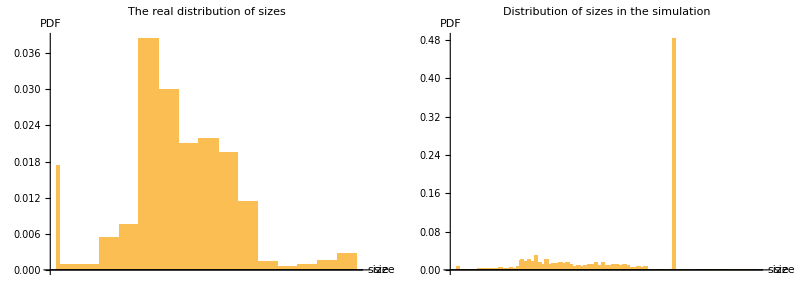

Part::partw: Part 1 of {} does not exist.

Last::nolast: {} has zero length and no last element.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

ToExpression::notstrbox: Last[{}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 1.06643 | 1.26905
100 | 0.589785 | 0.740922
150 | 1.15257 | 0.
200 | 3.92975 | 3.35444
300 | 7.16187 | 5.27041
500 | 100 (1-0.878145 Min[1.0222,$Failed]) | 6.97562
800 | 14.3871 | 16.6762
1000 | 14.3551 | 29.2837

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\traffic B hadoop\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B  Estimate Rate Window: 0.5 ms

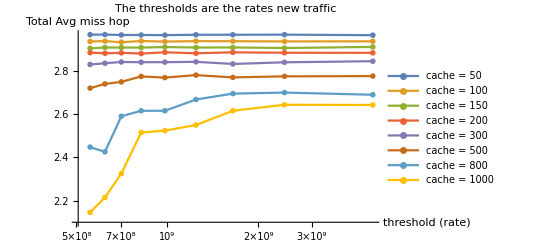

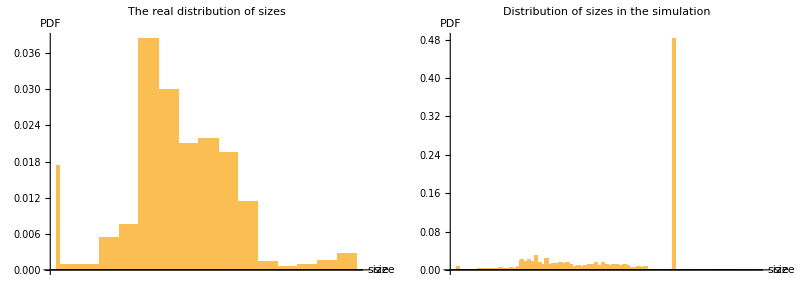

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi will be suppressed during this calculation.

cache size | Improvement in miss count (in percentages) | Improvement in bandwidth to controller (in percentages)
50 | 0.0841415 | 100 (1-1/($Failed)4.02376×10^6 Min[2.44499×10^-7 $Failed,2.47341×10^-7 $Failed,2.48524×10^-7 $Failed,2.48685×10^-7 $Failed,2.49394×10^-7 $Failed,2.50277×10^-7 $Failed,2.53883×10^-7 $Failed,2.56549×10^-7 $Failed,2.56622×10^-7 $Failed])
100 | 0.122385 | 100 (1-1/($Failed)4.00418×10^6 Min[2.4456×10^-7 $Failed,2.4682×10^-7 $Failed,2.48536×10^-7 $Failed,2.48852×10^-7 $Failed,2.49739×10^-7 $Failed,2.50101×10^-7 $Failed,2.53943×10^-7 $Failed,2.56077×10^-7 $Failed,2.60795×10^-7 $Failed])
150 | 0. | 100 (1-1/($Failed)3.98603×10^6 Min[2.45388×10^-7 $Failed,2.46992×10^-7 $Failed,2.48281×10^-7 $Failed,2.49419×10^-7 $Failed,2.49744×10^-7 $Failed,2.50354×10^-7 $Failed,2.50876×10^-7 $Failed,2.51407×10^-7 $Failed,2.52503×10^-7 $Failed])
200 | 0.142685 | 100 (1-1/($Failed)4.02487×10^6 Min[2.43962×10^-7 $Failed,2.47067×10^-7 $Failed,2.48455×10^-7 $Failed,2.49403×10^-7 $Failed,2.49761×10^-7 $Failed,2.51743×10^-7 $Failed,2.52415×10^-7 $Failed,2.53034×10^-7 $Failed,2.53349×10^-7 $Failed])
300 | 0. | 100 (1-1.2029 Min[0.831323,2.46709×10^-7 $Failed,2.48402×10^-7 $Failed,2.4899×10^-7 $Failed,2.49294×10^-7 $Failed,2.52632×10^-7 $Failed,2.53779×10^-7 $Failed,2.56644×10^-7 $Failed])
500 | 0. | 100 (1-1.31243 Min[0.761944,2.46796×10^-7 $Failed,2.471×10^-7 $Failed,2.48161×10^-7 $Failed,2.5232×10^-7 $Failed,2.55151×10^-7 $Failed])
800 | 0.889042 | 100 (1-1.55951 Min[0.629677,2.49611×10^-7 $Failed,2.52265×10^-7 $Failed])
1000 | 0. | 100 (1-1.83867 Min[0.543872,2.45761×10^-7 $Failed])

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\estimate rate 0.5m\\end time = 3.006s rate = 400M const size distribution = i-hadoop cache size = AAA push threasholds = BBB\\scalar-file.sca",{50,100,150,200,300,500,800,1000}, Sort[{555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

Rates: 2.5G Avg      Traffic: Traffic B   Rate estimator

1

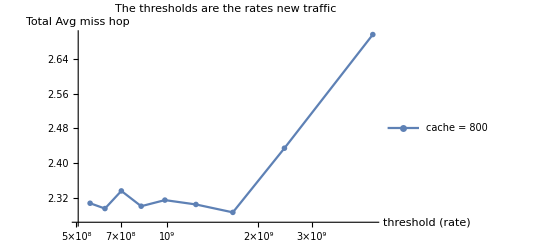

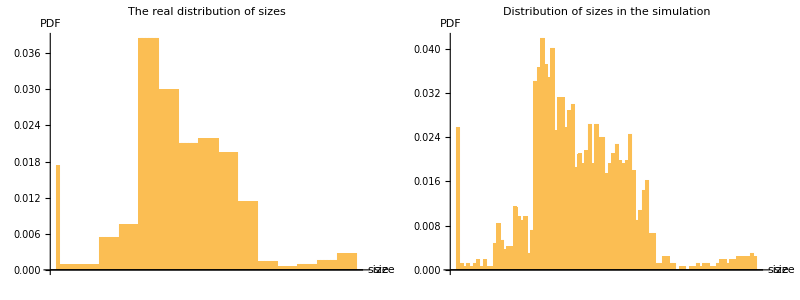

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\rate estimator check traffic A\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

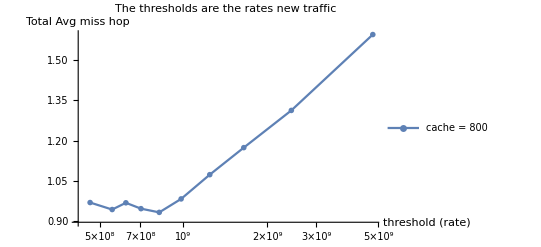

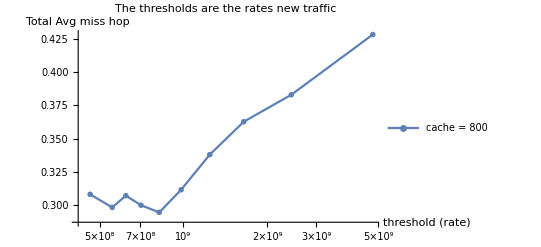

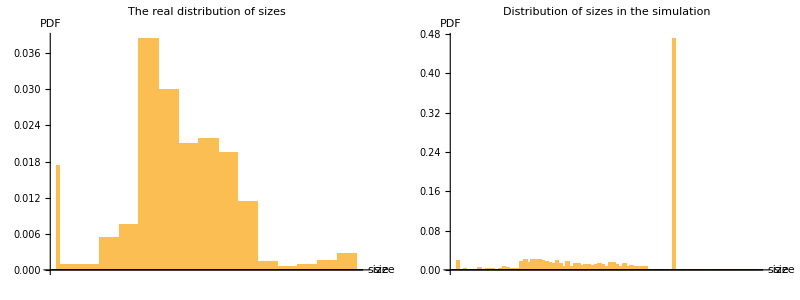

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
800 | 3.78873 | 818901538 | 4.42558 | 818901538

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\port-dest th with window2\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{800}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

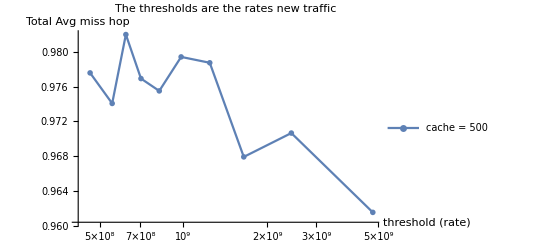

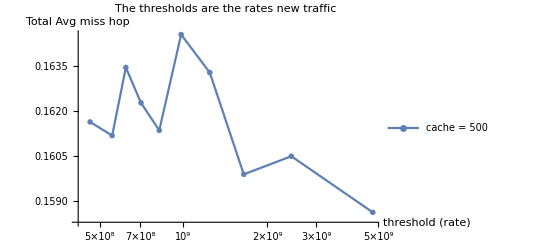

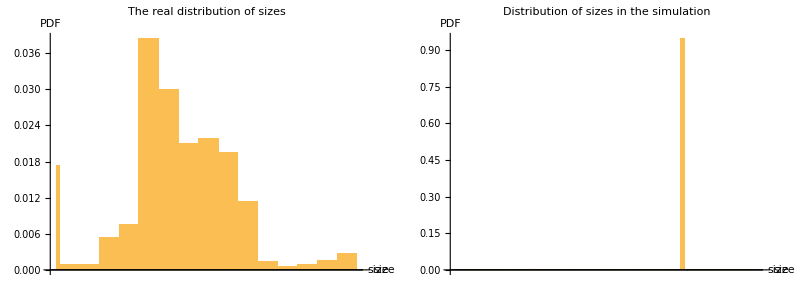

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
500 | 1.64047 | 4777534806 | 1.87607 | 4777534806

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\const rate B\\without window\\end time = 3.06s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{0,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

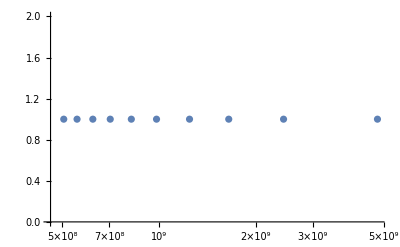

```mathematica
ListLogLinearPlot[Map[{#,1}&,{555037325/1.1,555037325,621504292,704099360,818901538,980967951,1242635857,1645830947,2437615808,4777534806}]]
```

```mathematica
Ordering
```

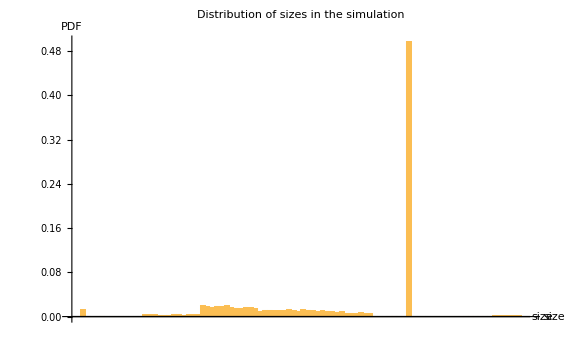

```mathematica
41000000000//N
```

4.1×10^10

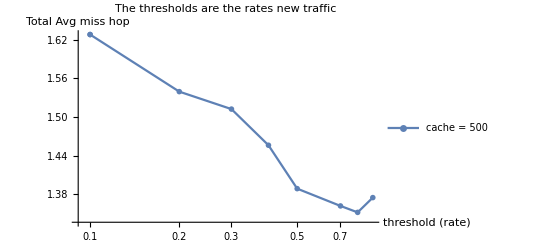

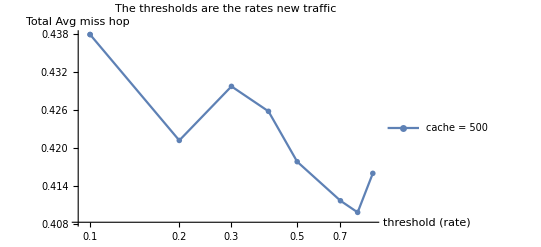

-Graphics-

cache size | Improvement in miss count (in percentages) | Optimal threshold by miss hop | Improvement in bandwidth to controller (in percentages) | Optimal threshold by bandwidth to controller
500 | 16.9538 | 0.8 | 6.38472 | 0.8

```mathematica
plotResults["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results\\test\\without window\\traffic c2\\end time = 3.006s rate = 2.5G cache size = AAA push threasholds = BBB\\scalar-file.sca",{500}, Sort[{0.1,0.2,0.3,0.4,0.5,0.7,0.8,0.9,0.1}]]
```

```mathematica
getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.06s rate = 2.5G cacheAgg = 10000 cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca"]
```

0.0012591

```mathematica
getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.06s rate = 2.5G cacheAgg = 3000 cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca",3]
```

0.328357

Traffic | size (B) | rate (b) | address space
A | 4*10^6 | 2.5*10^9*4 | 100*10^8
B | 4*10^6 | (2.5*SuperscriptBox[10, 9])/4 | 6000

20 Racks
th = 2.5*10^9 in both switches
ToR cache size = 200
controller switch cache size = 10000

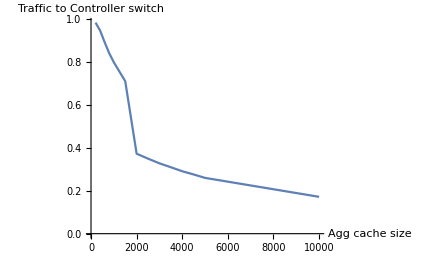

27% improvement when Agg cache size = 3000 compared to the corresponding fast cache

```mathematica
{{"Traffic", "size (B)", "rate (b)", "address space"}, {"A", "4*10^6", "2.5*10^9*4", "100*10^8"}, {"B", "4*10^6", "(2.5*SuperscriptBox[10, 9])/4", "6000"}}
Print["20 Racks\nth = 2.5*10^9 in both switches\nToR cache size = 200\ncontroller switch cache size = 10000"]
ListPlot[Map[({#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.06s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca",2]})&,{200,400,600,800,1000}]~Join~Map[({#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.06s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca",3]})&,{1500,2000,2500,3000,3500,4000,4500,5000,10000}],Joined->True,AxesLabel->{"Agg cache size","Traffic to Controller switch"}]
Print["27% improvement when Agg cache size = 3000 compared to the corresponding fast cache"]
```

```mathematica
range = 2000;
living = (4*10^6*8)/(2.5*10^9/4)*1/(40*10^-6)//Round
numOfToRs =20;
Print["Number of overlapping type B flows in a single Rack: ",(Select[SortBy[Tally[RandomChoice[Range[range],living]],Last],(Last[#]≥4)&]//Length)/living*100//N ]
Print["Number of overlapping type B flows in aggregation switch: ",(Select[SortBy[Tally[RandomChoice[Range[range],numOfToRs *living]],Last],(Last[#]≥4)&]//Length)/range*100//N]
```

1280

Number of overlapping type B flows in a single Rack: 0.546875

Number of overlapping type B flows in aggregation switch: 99.85

```mathematica
Map[({#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\new check all caches\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 10000 push threasholds = 2.5e9\\scalar-file.sca",2]})&,{200,400,600,800,1000,1200,1400,1600,1800,2000,1500,2000,2500,3000,3500,4000,4500,5000,6000,7000,8000,9000,10000}]
```

{{200,0.977793},{400,0.938589},{600,0.873522},{800,0.807712},{1000,0.753438},{1200,0.702943},{1400,0.6546},{1600,0.608324},{1800,0.262059},{2000,0.15539},{1500,0.628004},{2000,0.15539},{2500,0.126172},{3000,0.107909},{3500,0.0934793},{4000,0.0805421},{4500,0.0734462},{5000,0.0633012},{6000,0.0427553},{7000,0.015244},{8000,0.00584912},{9000,0.00539509},{10000,0.00553234}}

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\test\check all caches\end time = 3.006s rate = 2.5G cacheAgg = 6000 cacheToR = 200 push threasholds = 2.5e9\scalar-file.sca not found during Import.

Part::partw: Part 1 of {} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	2	].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	2	].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	2	].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\test\check all caches\end time = 3.006s rate = 2.5G cacheAgg = 6000 cacheToR = 250 push threasholds = 2.5e9\scalar-file.sca not found during Import.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\test\check all caches\end time = 3.006s rate = 2.5G cacheAgg = 6000 cacheToR = 300 push threasholds = 2.5e9\scalar-file.sca not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

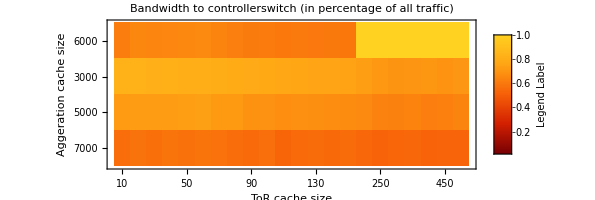

```mathematica
sizesAgg={6000,3000,5000,7000};
sizesToR = {10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,200,250,300,350,400,450,500};
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#1]<>" cacheToR = "<>ToString[#2]<>" push threasholds = 2.5e9\\scalar-file.sca",component])&,sizesAgg,sizesToR];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in percentage of all traffic)",FrameLabel->{{"ToR cache size",None},{"Aggeration cache size",None}},FrameTicks->{{Transpose[{Range[Length[sizesAgg]],sizesAgg}],None},{Transpose[{Range[Length[sizesToR]],sizesToR}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
```

```mathematica
{{"Traffic", "size (B)", "rate (b)", "address space"}, {"A", "4*10^6", "2.5*10^9*4", "100*10^8"}, {"B", "4*10^6", "(2.5*SuperscriptBox[10, 9])/4", "2000"}}
Print["20 Racks\nth = 2.5*10^9 in both switches measured from the 10^th packet"]
```

Traffic | size (B) | rate (b) | address space
A | 4*10^6 | 2.5*10^9*4 | 100*10^8
B | 4*10^6 | (2.5*SuperscriptBox[10, 9])/4 | 2000

20 Racks
th = 2.5*10^9 in both switches measured from the 10^th packet

Performance of the push as a function of the Aggregation cache size:

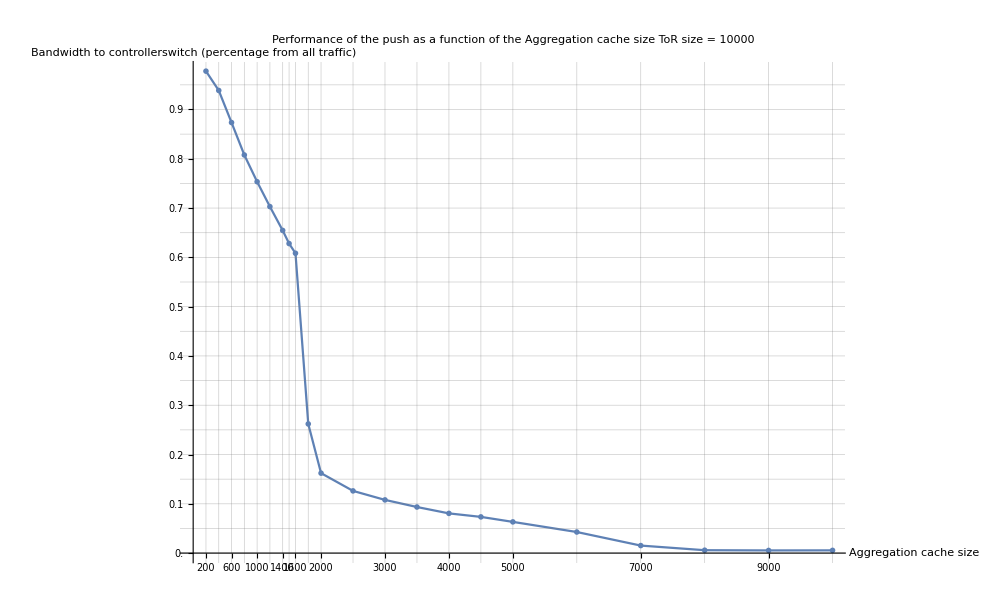

```mathematica
s={200,400,600,800,1000,1200,1400,1500,1600,1800,2000,2500,3000,3500,4000,4500,5000,6000,7000,8000,9000,10000};
ListPlot[Map[(temp ={#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check size Agg\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 10000 push threasholds = 2.5e9\\scalar-file.sca",2]};Tooltip[temp,temp])&,s] ,Joined->True,AxesLabel->{"Aggregation cache size","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Performance of the push as a function of the Aggregation cache size \n ToR size = 10000",GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

Performance of the push as a function of the ToR cache size:

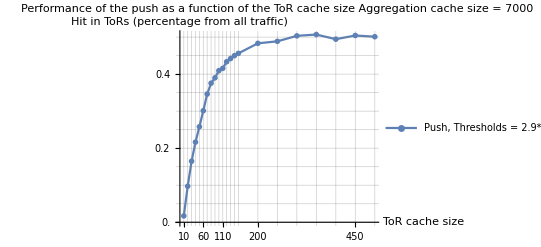

```mathematica
s={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,200,250,300,350,400,450,500};
ListPlot[Map[(temp ={#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\check all caches\\end time = 3.006s rate = 2.5G cacheAgg = 7000 cacheToR = "<>ToString[#]<>" push threasholds = 2.5e9\\scalar-file.sca",0]};Tooltip[temp,temp])&,{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,200,250,300,350,400,450,500}] ,Joined->True,AxesLabel->{"ToR cache size","Hit in ToRs \n(percentage from all traffic)"},PlotLabel->"Performance of the push as a function of the ToR cache size \n Aggregation cache size = 7000",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache"},GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

comparing Push to Fast cache:

```mathematica
s={700,1400,2100,2800,3500,4200,4900,5600,6300,7000};
push = Map[(temp = {#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\final check\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca",2]};Tooltip[temp,temp])&,s];
fast = Map[(temp = {#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca",2]};Tooltip[temp,temp])&,s];
fast10 = Map[(temp = {#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 p = 0.5\\scalar-file.sca",2]};Tooltip[temp,temp])&,s];
ListPlot[{push,fast,fast10,Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[p]<>" cacheToR = 200 p = 0.5\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1.25e9\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[p]<>" cacheToR = 200 p = 0.5\\scalar-file.sca",2]}]],s]} ,Joined->True,AxesLabel->{"Aggregation cache size","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"comparing Push to Fast cache \n ToR size = 200",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)"},GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

-Graphics-

```mathematica
s={30,60,90,120,150,180,200,240,270,300};
push = Map[(temp = {#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\final check\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[#]<>" push threasholds = 2.5e9\\scalar-file.sca",2]};Tooltip[temp,temp])&,s];
fast = Map[(temp = {#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[#]<>" push threasholds = 2.5e9\\scalar-file.sca",2]};Tooltip[temp,temp])&,s];
ListPlot[{push,fast,Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.5\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.5\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1.25e9\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.5\\scalar-file.sca",2]}]],s]} ,Joined->True,AxesLabel->{"ToR cache size","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"comparing Push to Fast cache \n Aggregation size = 2800",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)"},GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

-Graphics-

```mathematica
s={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}  ;
ListPlot[{Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\push\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\fast\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\diff th in layers cosw = 1.25e9\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca",2]}]],s]},Joined->True,AxesLabel->{"probability of app A","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"comparing Push to Fast cache \n Aggregation size = 3000\nToR cache size = 300",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)"},GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic}]
```

-Graphics-

```mathematica
s={700,1400,2100,2800,3500,4200,4900,5600,6300,7000};
push = Map[(temp = {#,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\final check\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca"]};Tooltip[temp,temp])&,s];
fast = Map[(temp = {#,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 push threasholds = 2.5e9\\scalar-file.sca"]};Tooltip[temp,temp])&,s];
fast10 = Map[(temp = {#,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[#]<>" cacheToR = 200 p = 0.5\\scalar-file.sca"]};Tooltip[temp,temp])&,s];
ListPlot[{push,fast,fast10} ,Joined->True,AxesLabel->{"Aggregation cache size","Miss hop count"},PlotLabel->"comparing Push to Fast cache \n ToR size = 200",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet"},GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic}]



s={30,60,90,120,150,180,200,240,270,300};
push = Map[(temp = {#,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\final check\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[#]<>" push threasholds = 2.5e9\\scalar-file.sca"]};Tooltip[temp,temp])&,s];
fast = Map[(temp = {#,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[#]<>" push threasholds = 2.5e9\\scalar-file.sca"]};Tooltip[temp,temp])&,s];
ListPlot[{push,fast,Map[Function[p,Tooltip[{p,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\test\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.5\\scalar-file.sca"]}]],s]} ,Joined->True,AxesLabel->{"ToR cache size","Miss hop count"},PlotLabel->"comparing Push to Fast cache \n Aggregation size = 2800",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet"},GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic}]



s={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}  ;
ListPlot[{Map[Function[p,Tooltip[{p,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\push\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca"]}]],s],Map[Function[p,Tooltip[{p,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\fast\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca"]}]],s],Map[Function[p,Tooltip[{p,missCountAvg["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\Different mixes between the apps\\fast from 10\\end time = 3.006s rate = 2.5G cacheAgg = 3000 cacheToR = 300 p = "<>ToString[p]<>"\\scalar-file.sca"]}]],s]},Joined->True,AxesLabel->{"probability of app A","Miss hop count"},PlotLabel->"comparing Push to Fast cache \n Aggregation size = 3000\nToR cache size = 300",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet"},GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
s={30,60,90,120,150,180,200,240,270,300};
ListPlot[{Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 2.5e9\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\fast\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\fast 10\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 1\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[p,Tooltip[{p,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 1.25e9\\end time = 3.006s rate = 2.5G cacheAgg = 2800 cacheToR = "<>ToString[p]<>" p = 0.6\\scalar-file.sca",2]}]],s]} ,Joined->True,AxesLabel->{"ToR cache size","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n Aggregation  size = 2800",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)"},GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

-Graphics-

```mathematica
s={700,1400,2100,2800,3500,4200,4900,5600,6300,7000};

ListPlot[{Map[Function[u,Tooltip[{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 2.5e9\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[u]<>" cacheToR = 200 p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\fast\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[u]<>" cacheToR = 200 p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\fast 10\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[u]<>" cacheToR = 200 p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 1\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[u]<>" cacheToR = 200 p = 0.6\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\new traffic\\diff th in layers cosw = 1.25e9\\end time = 3.006s rate = 2.5G cacheAgg = "<>ToString[u]<>" cacheToR = 200 p = 0.6\\scalar-file.sca",2]}]],s]} ,Joined->True,AxesLabel->{"Aggregation cache size","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 200",PlotLegends->{"Push, Thresholds = 2.9*10^9","Fast cache","Fast cache from 10^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)"},GridLines->{s,Range[0,1,0.05]},PlotMarkers->"OpenMarkers",Ticks->{s,Range[0,1,0.05]}]
```

-Graphics-

Static configuration:

```mathematica
m=20;
Table[(
s = "C:\\Users\\0wner\\OneDrive - post.bgu.ac.il\\Desktop\\Traffics\\Traffic B"<>"\\traffic"<>ToString[j]<>".csv";
Subscript[rack, j]= StringSplit[Import[s,"List"],","];
Subscript[destinations, j]=Round[ToExpression[Subscript[rack, j][[All,3]]]];
Subscript[tor, j]=Take[Reverse[SortBy[Tally[Subscript[destinations, j]],Last]][[All,1]],100]
),{j,0,m-1}];
agg = Apply[Complement,{Apply[Union,Table[Subscript[destinations, i],{i,0,m-1}]]}~Join~Table[Subscript[tor, i],{i,0,m-1}]];
```

```mathematica
Subscript[tor, 5]
```

{98817836,98791572,97789343,94254512,94036940,92796858,91965284,91739807,90055289,88884243,85180963,84188040,83546082,82578138,82116576,81229751,81208553,80578798,79972932,72580337,72148745,70781620,69674695,69272112,66921428,58836281,57013071,55357373,54896260,51621451,47141897,46006892,39387202,39045377,35862737,33399719,30149959,27833095,27552304,26768898,25508702,24794134,24520794,24289079,20135987,17653083,16990209,15353375,12907546,10868290,10277896,9384596,8291323,5295953,4805277,3416809,1757154,90427,35614848,44641604,24658135,14521392,77734090,46919979,78119958,60525641,5008106,67768347,78258465,32175922,84534676,98516559,7261267,98593077,8959624,12418,91929260,46808056,50130513,46756704,78393390,50277028,37924790,7132438,47355943,59746029,76171157,90496204,96240553,16804900,42782612,75978370,54946535,79630138,93721861,67765702,851373,78771001,11925467,60676410}

```mathematica
agg//Length
```

4559

Various algorithms’ performance as a function of the number of packets from which decisions are made:

```mathematica
s={0,1,2,3,4,5,6,7,8,10,20,30,40,50};
alg = {"Fast n-th","Push th=(1,2.5e9)"};
algLable = {"Fast cache from n^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 2.5*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 0.625*10^9, Th in Agg sw = 2.5*10^9)"};
ListPlot[{Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Fast n-th\\end time = 3.006s rate = 2.5G  packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Push th = (1,2.5e9)\\end time = 3.006s rate = 2.5G  packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Push th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Push th = (1.25e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Push th = (0.625e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s]} ,Joined->True,Frame->True,FrameLabel->{"Number of packets from which decisions are made","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[algLable,Below],GridLines->{s+1,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s+1,Automatic},PlotRange->{{1,11},Automatic}]
```

-Graphics-

```mathematica
s={0,1,2,3,4,5,6,7,8,10};
algLable = {"Fast cache from n^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 2.5*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 0.625*10^9, Th in Agg sw = 2.5*10^9)"};
ListPlot[{Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\web search\\Fast n-th th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\web search\\Push th = (1,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\web search\\Push th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\web search\\Push th = (1.25e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s]} ,Joined->True,Frame->True,FrameLabel->{"Number of packets from which decisions are made","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Websearch rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Websearch) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[algLable,Below],GridLines->{s+1,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s+1,Automatic},PlotRange->{{1,11},Automatic}]
```

-Graphics-

```mathematica
s={0,1,2,3,4,5,6,7,8,10};
algLable = {"Fast cache from n^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 2.5*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 0.625*10^9, Th in Agg sw = 2.5*10^9)"};
ListPlot[{Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const traffic\\Fast n-th th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const traffic\\Push th = (1,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const traffic\\Push th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const traffic\\Push th = (1.25e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s]} ,Joined->True,Frame->True,FrameLabel->{"Number of packets from which decisions are made","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Websearch) rate = 2.5*10^9*4\nApp B: size = Avg(Websearch) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[algLable,Below],GridLines->{s+1,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s+1,Automatic},PlotRange->{{1,11},Automatic}]
```

-Graphics-

```mathematica
s={0,1,2,3,4,5,6,7,8,10};
algLable = {"Fast cache from n^th packet","Push: (Th in Controller sw = 1, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 2.5*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 1.25*10^9, Th in Agg sw = 2.5*10^9)","Push: (Th in Controller sw = 0.625*10^9, Th in Agg sw = 2.5*10^9)"};
ListPlot[{Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const size diff rate\\Fast n-th th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const size diff rate\\Push th = (1,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const size diff rate\\Push th = (2.5e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s],Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index (3000,300)\\Websearch const size diff rate\\Push th = (1.25e9,2.5e9)\\end time = 3.006s rate = 2.5G packet index = "<>ToString[u]<>"\\scalar-file.sca",2]}]],s]} ,Joined->True,Frame->True,FrameLabel->{"Number of packets from which decisions are made","Bandwidth to controllerswitch \n(percentage from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Websearch) rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Websearch) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[algLable,Below],GridLines->{s+1,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s+1,Automatic},PlotRange->{{1,11},Automatic}]
```

-Graphics-

```mathematica
ratesDistributionSamples=Table[g[1.0256410256410255,10^6,500],{j,10000}];
GraphicsGrid[{{Histogram[ratesDistributionSamples,"Log","LogProbability",FrameLabel->{"Rate (bps)","PDF (Histogram)"},Frame->True],descriptivestatistics@ratesDistributionSamples}},ImageSize->Full]
GraphicsGrid[{{Histogram[ratesDistributionSamples,FrameLabel->{"Rate (bps)","PDF (Histogram)"},Ticks->{None, Automatic},Frame->True],descriptivestatistics@ratesDistributionSamples}},ImageSize->Full]
```

-Graphics-

-Graphics-

```mathematica
s={0,1,2,3,4,5,6,7,8,10};

m = Map[Function[w,Map[Function[u,{w,u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map (3000,300)\\hadoop const size diff rate\\Fast n-th  packet decision index  (Agg,Con_SW) =  ("<>ToString[u]<>","<>ToString[w]<>")\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],s]],s];
ConAgg={0,1,2,3,4,5,6,7,8,10};
AggToR = {0,1,2,3,4,5,6,7,8,10};
component = 2;
data = (m[[All,All,3]]);
color = "SolarColors";
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)",FrameLabel->{{"Aggregation ToR",None},{"Controller switch to Aggregation",None}},FrameTicks->{{Transpose[{Range[Length[ConAgg]],ConAgg}],None},{Transpose[{Range[Length[AggToR]],AggToR}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
```

-Graphics-

```mathematica
Range[1,20,2]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
w=s[[2]];
u=s[[2]];
Map[Function[w,{w,u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map (3000,300)\\hadoop const size diff rate\\Fast n-th  packet decision index  (Agg,Con_SW) =  ("<>ToString[w]<>","<>ToString[u]<>")\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],s]
```

{{0,1,0.395072},{1,1,0.225784},{2,1,0.175676},{3,1,0.151022},{4,1,0.156683},{5,1,0.211183},{6,1,0.398169},{7,1,0.468569},{8,1,0.495813},{10,1,0.524314}}

```mathematica
Map[Function[u,Tooltip[{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Con_SW) =  ("<>ToString[u]<>",5)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}]],1,3,5,7,9,11,13,15,17,19]
```

Map::nonopt: Options expected (instead of 19) beyond position 3 in Map[Function[u,{u+1,getPercentageOfTrafficToComponent[C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\packet index heat-map - diversity (3000,300)\hadoop const size diff rate\diversity-Push  packet decision index  (diversity,Con_SW) =  (<>ToString[u]<>,5)\end time = 3.006s rate = 2.5G\scalar-file.sca,2]}],1,3,5,7,9,11,13,15,17,19]. An option must be a rule or a list of rules.

```mathematica
ListLinePlot[Map[Function[u,{u+1,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Con_SW) =  ("<>ToString[u]<>",5)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],{1,3,5,7,9,11,13,15,17,19}]]
```

-Graphics-

```mathematica
ListLinePlot[{Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Agg) =  ("<>ToString[u]<>",0)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],{1,3,5,7,9,11,13,15,17,19}],Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Agg) =  ("<>ToString[u]<>",1)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],{1,3,5,7,9,11,13,15,17,19}],Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Agg) =  ("<>ToString[u]<>",2)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],{1,3,5,7,9,11,13,15,17,19}],Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Agg) =  ("<>ToString[u]<>",3)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],{1,3,5,7,9,11,13,15,17,19}]},Frame->True,FrameLabel->{"Diversity Threshold","Bandwidth to controllerswitch \n(fraction from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Hadoop) rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[{"Count-Push Th = (5,0)","Count-Push Th = (5,1)","Count-Push Th = (5,2)","Count-Push Th = (5,3)"},Below],GridLines->{{1,3,5,7,9,11,13,15,17,19},Automatic},PlotMarkers->"OpenMarkers",Ticks->{{1,3,5,7,9,11,13,15,17,19},Automatic},PlotRange->All]
```

-Graphics-

```mathematica
getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\hadoop const size diff rate\\diversity-Push  packet decision index  (diversity,Agg) =  (1,2)\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]
```

0.0756851

```mathematica
s={1,3,5,7,9,11,13,15,17,19};
ListLinePlot[{Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\App A Hadoop App B Avg(Hadoop) diff rate in both apps\\diversity-Push  - diversityTh = "<>ToString[u]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],s]},Frame->True,FrameLabel->{"Diversity Threshold","Bandwidth to controllerswitch \n(fraction from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Hadoop) rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[{"Count-Push Th = (5,0)","Count-Push Th = (5,1)","Count-Push Th = (5,2)","Count-Push Th = (5,3)"},Below],GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic},PlotRange->All]
```

-Graphics-

```mathematica
s={1,3,5,7,9,11,13,15,17,19};
ListLinePlot[{Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\packet index heat-map - diversity (3000,300)\\App A Hadoop App B Avg(Hadoop) diff rate uniform\\diversity-Push  - diversityTh = "<>ToString[u]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],s]},Frame->True,FrameLabel->{"Diversity Threshold","Bandwidth to controllerswitch \n(fraction from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Hadoop) rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[{"Count-Push Th = (5,0)","Count-Push Th = (5,1)","Count-Push Th = (5,2)","Count-Push Th = (5,3)"},Below],GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic},PlotRange->All]
```

-Graphics-

```mathematica
s={1,3,5,7,9,11,13,15,17,19};
ListLinePlot[{Map[Function[u,{u,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B 6000 diff rate\\diversity-Push  - diversityTh = "<>ToString[u]<>" p = 0.6\\end time = 3.006s rate = 2.5G\\scalar-file.sca",2]}],s]},Frame->True,FrameLabel->{"Diversity Threshold","Bandwidth to controllerswitch \n(fraction from all traffic)"},PlotLabel->"Traffic:\nApp A: size = Avg(Hadoop) rate = is drawn with avg = 2.5*10^9*4\nApp B: size = 6000 rate = (2.5*SuperscriptBox[10, 9])/4 \n ToR size = 300, Aggregation = 3000",PlotLegends->Placed[{"Count-Push Th = (5,0)","Count-Push Th = (5,1)","Count-Push Th = (5,2)","Count-Push Th = (5,3)"},Below],GridLines->{s,Automatic},PlotMarkers->"OpenMarkers",Ticks->{s,Automatic},PlotRange->All]
```

-Graphics-

Comparing 1-Diversity Threshold on various traffics:

Traffic:
App A: size  = Hadoop , rate is drawn with avg = 2.5*10^9*4
App B: size  = Avg(Hadoop) , rate is drawn with avg = (2.5*10^9)/4

```mathematica
divTh={1,3,5,7,9,11,13,15,17,19};
probA = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B avg(Hadoop) diff rate\\diversity-Push  - diversityTh = "<>ToString[#1]<>" p = "<>ToString[#2]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",component])&,divTh,probA];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4",FrameLabel->{{"Probability of App A",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[probA]],probA}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
data
Print["The improvement ratio from fast cache in each traffic:\n",{Map[(Last[#]/(#[[1]]))&,Transpose[data]]}//TableForm]
ListLinePlot[{Table[{probA[[i]],Max[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],Min[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],data[[All,i]][[1]]},{i,1,Length[probA]}],Table[{probA[[i]],Last[data[[All,i]]]},{i,1,Length[probA]}]},GridLines->{probA,Automatic},PlotMarkers->"OpenMarkers",Ticks->{probA,Automatic},PlotRange->All,PlotLegends->{"The worst Diversity Th","The Best Diversity Th","1-Diversity Th","Fast cache"},Frame->True,FrameLabel->{"Probability of App A","Bandwidth to controllerswitch \n(in fraction of all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4"]
```

-Graphics-

{{0.00102924,0.00311441,0.00560897,0.00913538,0.0143742,0.0321729,0.0822084,0.131538,0.158352,0.158235,0.129543},{0.00101972,0.00294199,0.010874,0.0664556,0.129575,0.187297,0.212668,0.211769,0.196959,0.172792,0.136997},{0.00102879,0.0398507,0.199705,0.29312,0.359022,0.39516,0.405328,0.370266,0.293669,0.191322,0.130338},{0.00103477,0.0641198,0.22619,0.319791,0.387769,0.40918,0.418881,0.378971,0.295778,0.196773,0.137879},{0.00103875,0.0883527,0.23334,0.322179,0.38471,0.410146,0.420927,0.387189,0.292789,0.194901,0.135552},{0.00102772,0.0997527,0.237798,0.325378,0.388523,0.412124,0.418769,0.38158,0.303265,0.196904,0.129823},{0.0010353,0.0915979,0.238043,0.331449,0.393364,0.414426,0.420907,0.379177,0.29381,0.200986,0.136117},{0.00102575,0.105605,0.240584,0.333909,0.393985,0.408441,0.41631,0.377523,0.292239,0.193145,0.133237},{0.00103471,0.113929,0.240513,0.339764,0.388865,0.42135,0.416462,0.380105,0.303624,0.195539,0.128164},{0.00101837,0.111331,0.245755,0.332418,0.388836,0.410382,0.420535,0.377224,0.298809,0.19459,0.128321}}

The improvement ratio from fast cache in each traffic:
0.989434 | 35.7472 | 43.8146 | 36.388 | 27.0509 | 12.7555 | 5.11547 | 2.8678 | 1.887 | 1.22975 | 0.990567

-Graphics-

Traffic:
App A: size  = Hadoop , rate is drawn (uniform) with avg = 2.5*10^9*4
App B: size  = Avg(Hadoop) , rate is drawn (uniform) with avg = (2.5*10^9)/4

```mathematica
divTh={1,3,5,7,9,11,13,15,17,19};
probA = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B avg(hadoop) diff rate uniform\\diversity-Push  - diversityTh = "<>ToString[#1]<>" p = "<>ToString[#2]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",component])&,divTh,probA];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn (uniform)with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate (uniform) with avg= (2.5*SuperscriptBox[10, 9])/4",FrameLabel->{{"Probability of App A",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[probA]],probA}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
data
Print["The improvement ratio from fast cache in each traffic:\n",{Map[(Last[#]/(#[[1]]))&,Transpose[data]]}//TableForm]
ListLinePlot[{Table[{probA[[i]],Max[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],Min[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],data[[All,i]][[1]]},{i,1,Length[probA]}],Table[{probA[[i]],Last[data[[All,i]]]},{i,1,Length[probA]}]},GridLines->{probA,Automatic},PlotMarkers->"OpenMarkers",Ticks->{probA,Automatic},PlotRange->All,PlotLegends->{"The worst Diversity Th","The Best Diversity Th","1-Diversity Th","Fast cache"},Frame->True,FrameLabel->{"Probability of App A","Bandwidth to controllerswitch \n(in fraction of all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn (uniform)with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate (uniform) with avg= (2.5*SuperscriptBox[10, 9])/4"]
```

-Graphics-

{{0.00103455,0.00298775,0.0056966,0.00871649,0.0137798,0.026861,0.0510966,0.0757108,0.0802932,0.0762092,0.0454955},{0.00103295,0.00287161,0.00939964,0.0870013,0.130717,0.139403,0.135251,0.132578,0.126762,0.104207,0.0474179},{0.00102364,0.0323731,0.149453,0.216054,0.257447,0.277613,0.272296,0.24474,0.190324,0.118683,0.0483177},{0.0010321,0.0488074,0.164529,0.242244,0.282202,0.306725,0.292077,0.259742,0.195949,0.123986,0.0471254},{0.00102972,0.0686609,0.179653,0.251073,0.292958,0.308365,0.291649,0.256001,0.193569,0.127202,0.0473708},{0.00103236,0.0773594,0.183729,0.263059,0.304897,0.314532,0.300764,0.260423,0.198634,0.12256,0.0468681},{0.00103401,0.0747464,0.195555,0.264649,0.303045,0.315791,0.304222,0.259835,0.196877,0.123669,0.0464646},{0.0010185,0.0758963,0.187862,0.266206,0.300551,0.31291,0.306565,0.263786,0.197039,0.125902,0.0509638},{0.00101527,0.0839718,0.199074,0.267607,0.302521,0.314855,0.307272,0.267449,0.195535,0.123345,0.0485196},{0.00103059,0.0794054,0.197599,0.2675,0.302146,0.313969,0.299245,0.257654,0.197942,0.122062,0.0470136}}

The improvement ratio from fast cache in each traffic:
0.996179 | 26.577 | 34.6872 | 30.6889 | 21.9268 | 11.6887 | 5.85646 | 3.40313 | 2.46524 | 1.60167 | 1.03337

-Graphics-

Traffic:
App A: size  = Hadoop , rate is drawn with avg = 2.5*10^9*4
App B: size  = 150000 , rate is drawn with avg = (2.5*10^9)/4

```mathematica
divTh={1,3,5,7,9,11,13,15,17,19};
probA = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B 150000 diff rate\\diversity-Push  - diversityTh = "<>ToString[#1]<>" p = "<>ToString[#2]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",component])&,divTh,probA];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = 150000 rate with avg= (2.5*SuperscriptBox[10, 9])/4",FrameLabel->{{"Probability of App A",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[probA]],probA}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
data
Print["The improvement ratio from fast cache in each traffic:\n",{Map[(Last[#]/(#[[1]]))&,Transpose[data]]}//TableForm]
ListLinePlot[{Table[{probA[[i]],Max[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],Min[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],data[[All,i]][[1]]},{i,1,Length[probA]}],Table[{probA[[i]],Last[data[[All,i]]]},{i,1,Length[probA]}]},GridLines->{probA,Automatic},PlotMarkers->"OpenMarkers",Ticks->{probA,Automatic},PlotRange->All,PlotLegends->{"The worst Diversity Th","The Best Diversity Th","1-Diversity Th","Fast cache"},Frame->True,FrameLabel->{"Probability of App A","Bandwidth to controllerswitch \n(in fraction of all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = 150000 rate with avg= (2.5*SuperscriptBox[10, 9])/4"]
```

-Graphics-

{{0.00102298,0.138431,0.16123,0.156298,0.156484,0.149168,0.147639,0.136167,0.130346,0.135914,0.132399},{0.00102176,0.218809,0.188041,0.176677,0.153412,0.151173,0.150312,0.138834,0.140776,0.135254,0.126787},{0.00101652,0.358231,0.235946,0.185319,0.170601,0.151474,0.145749,0.141086,0.134177,0.132302,0.132926},{0.00102993,0.366298,0.242825,0.189854,0.16298,0.152124,0.143698,0.141525,0.134609,0.135598,0.135084},{0.00103169,0.369999,0.234829,0.185985,0.159318,0.155313,0.148994,0.146512,0.128099,0.136188,0.132689},{0.00102553,0.351883,0.243421,0.180678,0.166426,0.154384,0.147416,0.137711,0.14024,0.132282,0.133319},{0.00102043,0.365078,0.232058,0.190892,0.165784,0.155857,0.144071,0.139531,0.137533,0.129332,0.129719},{0.00102269,0.369556,0.241296,0.182775,0.168139,0.155702,0.141395,0.139613,0.129932,0.131811,0.129907},{0.00102896,0.367325,0.23458,0.187051,0.164161,0.15481,0.149337,0.134362,0.139157,0.126696,0.13272},{0.00102721,0.35747,0.243034,0.188687,0.161348,0.150589,0.13788,0.137835,0.137269,0.131458,0.128173}}

The improvement ratio from fast cache in each traffic:
1.00414 | 2.5823 | 1.50738 | 1.20723 | 1.03108 | 1.00953 | 0.933899 | 1.01225 | 1.05312 | 0.967216 | 0.968082

-Graphics-

Traffic:
App A: size  = Hadoop , rate is drawn with avg = 2.5*10^9*4
App B: size  = 1000 , rate is drawn with avg = (2.5*10^9)/4

```mathematica
divTh={1,3,5,7,9,11,13,15,17,19};
probA = {0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};(*0*)
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B 1000 diff rate\\diversity-Push  - diversityTh = "<>ToString[#1]<>" p = "<>ToString[#2]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",component])&,divTh,probA];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = 1000 rate with avg= (2.5*SuperscriptBox[10, 9])/4",FrameLabel->{{"Probability of App A",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[probA]],probA}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
data
Print["The improvement ratio from fast cache in each traffic:\n",{Map[(Last[#]/(#[[1]]))&,Transpose[data]]}//TableForm]
ListLinePlot[{Table[{probA[[i]],Max[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],Min[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],data[[All,i]][[1]]},{i,1,Length[probA]}],Table[{probA[[i]],Last[data[[All,i]]]},{i,1,Length[probA]}]},GridLines->{probA,Automatic},PlotMarkers->"OpenMarkers",Ticks->{probA,Automatic},PlotRange->{0.08,0.23},PlotLegends->{"The worst Diversity Th","The Best Diversity Th","1-Diversity Th","Fast cache"},Frame->True,FrameLabel->{"Probability of App A","Bandwidth to controllerswitch \n(in fraction of all traffic)"},PlotLabel->"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = 1000 rate with avg= (2.5*SuperscriptBox[10, 9])/4"]
```

-Graphics-

{{0.131093,0.130364,0.129681,0.130879,0.140913,0.133517,0.140113,0.129934,0.132497,0.129543},{0.130739,0.131292,0.131821,0.134239,0.130821,0.124097,0.128823,0.134981,0.13109,0.136997},{0.133611,0.138371,0.132317,0.129784,0.1392,0.12314,0.129453,0.127205,0.130405,0.130338},{0.132732,0.13349,0.123464,0.133254,0.128459,0.129934,0.131709,0.133564,0.12814,0.137879},{0.127162,0.136287,0.132982,0.134238,0.13323,0.131467,0.134783,0.134939,0.130103,0.135552},{0.128648,0.12895,0.133093,0.128072,0.129659,0.133546,0.126895,0.132067,0.12773,0.129823},{0.130974,0.130401,0.134645,0.133623,0.129462,0.132897,0.130703,0.134414,0.130433,0.136117},{0.131975,0.137012,0.126424,0.132366,0.127191,0.126523,0.133171,0.133079,0.135292,0.133237},{0.135197,0.1255,0.127338,0.125996,0.134612,0.131612,0.134318,0.127445,0.136991,0.128164},{0.14068,0.127912,0.134655,0.127323,0.135687,0.12648,0.130206,0.129438,0.127645,0.128321}}

The improvement ratio from fast cache in each traffic:
1.07314 | 0.981188 | 1.03835 | 0.972826 | 0.962908 | 0.9473 | 0.929293 | 0.996179 | 0.963379 | 0.990567

-Graphics-

Traffic:
App A and App A with the same size and same rates (drawn from the same distribution)

```mathematica
divTh={1,3,5,7,9,11,13,15,17,19};
probA = {0,0.1,0.2,0.3,0.4,0.5};(*0.6,0.7,0.8,0.9,1*)
component = 2;
color = "SolarColors";
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\diversity th and prob B and A -  (3000,300)\\App A Hadoop App B Hadoop equal rates\\diversity-Push  - diversityTh = "<>ToString[#1]<>" p = "<>ToString[#2]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",component])&,divTh,probA];
plot = MatrixPlot[data,PlotLabel->"Bandwidth to controllerswitch \n(in fraction of all traffic)\nTraffic:\nSame size (Hadoop) same rates (drawn from same distribution)",FrameLabel->{{"Probability of App A",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[probA]],probA}],None}},ColorFunction->color];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
Legended[plot,legend]
data //TableForm
Print["The improvement ratio from fast cache in each traffic:\n",{Map[(Last[#]/(#[[1]]))&,Transpose[data]]}//TableForm]
ListLinePlot[{Table[{probA[[i]],Max[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],Min[data[[All,i]]]},{i,1,Length[probA]}],Table[{probA[[i]],data[[All,i]][[1]]},{i,1,Length[probA]}],Table[{probA[[i]],Last[data[[All,i]]]},{i,1,Length[probA]}]},GridLines->{probA,Automatic},PlotMarkers->"OpenMarkers",Ticks->{probA,Automatic},PlotRange->All,PlotLegends->{"The worst Diversity Th","The Best Diversity Th","1-Diversity Th","Fast cache"},Frame->True,FrameLabel->{"Probability of App A","Bandwidth to controllerswitch \n(in fraction of all traffic)"},PlotLabel->"Traffic:\nSame size (Hadoop) same rates (drawn from same distribution)"]
```

-Graphics-

0.00101384 | 0.271041 | 0.437375 | 0.313229 | 0.24643 | 0.20487
0.00101624 | 0.256516 | 0.334501 | 0.257029 | 0.223895 | 0.19642
0.00101791 | 0.282537 | 0.368735 | 0.271477 | 0.234484 | 0.214855
0.00101313 | 0.288433 | 0.376302 | 0.278462 | 0.241322 | 0.218526
0.0010159 | 0.295808 | 0.372328 | 0.278669 | 0.24503 | 0.221834
0.00102282 | 0.289101 | 0.376876 | 0.286543 | 0.251042 | 0.223626
0.00100874 | 0.296108 | 0.380587 | 0.286466 | 0.258191 | 0.226629
0.000999862 | 0.297619 | 0.379031 | 0.285638 | 0.250818 | 0.224248
0.00101734 | 0.297378 | 0.373423 | 0.286206 | 0.252825 | 0.225473
0.0010245 | 0.296948 | 0.381199 | 0.28912 | 0.25174 | 0.225177

The improvement ratio from fast cache in each traffic:
1.01051 | 1.09558 | 0.871561 | 0.923031 | 1.02155 | 1.09912

-Graphics-

```mathematica
Map[getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller diversity th and prob B and A -  (3000,300)\\App A Hadoop App B Hadoop equal rates\\non Push  - diversityTh = 1 p = "<>ToString[#]<>"\\end time = 3.006s rate = 2.5G\\scalar-file.sca",3]&,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}]
```

{0.00124026,0.00157273,0.00200182,0.00236022,0.00272696,0.00308255,0.00335195,0.0037971,0.00421857,0.0045422,0.00463633}

```mathematica
ListLinePlot[Map[Tooltip[{#,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller diversity th and prob B and A -  (3000,300)\\App A Hadoop rate drawn avg = 2.5e9 4 App B avg(Hadoop) rate drawn avg = 2.5e9 d 4\\non Push p = "<>ToString[#]<>"\\end time = 3.006s\\scalar-file.sca",3]}]&,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}],PlotMarkers->"OpenMarkers"]
```

-Graphics-

```mathematica
Select[Flatten[Outer[{#1,#2,#3,getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\non Push p = "<>ToString[#1]<>" diversityTh = "<>ToString[#3]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s\\scalar-file.sca",3]}&,{0,0.2,0.4,0.6,0.8,1},{0,2,4,5,6,7,10},{0,1,2,3,4,5,10,15,19}],2],(Last[#]<1)&][[All,1;;3]]//Length
```

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\controller counter and diversity th-(3000,300)\non Push p = 0 diversityTh = 15 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\end time = 3.006s\scalar-file.sca not found during Import.

Part::partw: Part 1 of {} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	3	].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	3	].

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[Symbol[],bin	3	].

General::stop: Further output of StringContainsQ::strse will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\controller counter and diversity th-(3000,300)\non Push p = 0 diversityTh = 19 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\end time = 3.006s\scalar-file.sca not found during Import.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Symbol[]].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

ToExpression::notstrbox: Symbol[] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Import::nffil: File C:\omnetpp-5.6.1\samples\CacheSimulation\simulations\my_results1\controller counter and diversity th-(3000,300)\non Push p = 0 diversityTh = 10 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\end time = 3.006s\scalar-file.sca not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

253

```mathematica
Flatten
```

ToR = 300

```mathematica
divTh=Reverse[{0,1,2,3,4,5}];
countTH = {0,2,4,6,8};(*0*)
component = 3;
color = "SolarColors";
ToRCacheSize = 300;
ff = Map[Function[p,
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\non Push p = "<>ToString[p]<>" diversityTh = "<>ToString[#1]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",component])&,divTh,countTH];
f[x_]:=ColorData["SolarColors"][1-x];
legend=BarLegend[{Reverse[Map[f,Reverse[Sort[Flatten[data]]]]],MinMax[data]},LegendLabel->"Legend Label"];
plot = MatrixPlot[data,ColorFunction->f,ColorFunctionScaling->False,PlotLabel->"Bandwidth to controller \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p],FrameLabel->{{"Count Threshold",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[countTH]],countTH}],None}}];
Grid[{{Legended[Grid[{{plot,Labeled["Fast",getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\cFast p = "<>ToString[p]<>" diversityTh = 0 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]//Quiet]}}],legend],data//MatrixForm}}]
],{0,0.25,0.5,0.75,1}]
(*getPercentageOfTrafficToComponent["",3]*)
```

{-Graphics- | Fast0.00123541 | (0.00167108 | 0.00299644 | 0.00597571 | 0.0090587 | 0.012243
0.00152318 | 0.00274164 | 0.00545987 | 0.00825551 | 0.0112048
0.00136536 | 0.00242585 | 0.00489396 | 0.00746022 | 0.0100191
0.00122613 | 0.0020535 | 0.00415301 | 0.00644489 | 0.00867824
0.00109108 | 0.00167112 | 0.00321538 | 0.00491798 | 0.00667621
0.0011133 | 0.00164153 | 0.00320717 | 0.00491126 | 0.00663876),-Graphics- | Fast0.234706 | (0.0030367 | 0.00462089 | 0.00776846 | 0.0111576 | 0.0149758
0.00262691 | 0.00406405 | 0.00705422 | 0.0100667 | 0.0135894
0.00239209 | 0.00362975 | 0.006359 | 0.00930756 | 0.0120641
0.00203201 | 0.00313062 | 0.00554128 | 0.00822687 | 0.0109359
0.360859 | 0.359131 | 0.347678 | 0.351827 | 0.339178
0.367296 | 0.360236 | 0.357594 | 0.343068 | 0.328119),-Graphics- | Fast0.363674 | (0.00759564 | 0.0108522 | 0.0165365 | 0.0217424 | 0.0272908
0.0082497 | 0.0108357 | 0.015253 | 0.0208706 | 0.0256399
0.00691695 | 0.0101876 | 0.0132618 | 0.0180077 | 0.0250641
0.00711328 | 0.00991811 | 0.0151404 | 0.0180757 | 0.0206755
0.557268 | 0.552113 | 0.548165 | 0.538225 | 0.539299
0.562429 | 0.550852 | 0.553874 | 0.536701 | 0.528916),-Graphics- | Fast0.405035 | (0.155557 | 0.151092 | 0.0855334 | 0.142318 | 0.152061
0.162999 | 0.117562 | 0.076222 | 0.151187 | 0.155259
0.147849 | 0.135749 | 0.0744217 | 0.150845 | 0.146659
0.155888 | 0.121854 | 0.0711635 | 0.169209 | 0.150214
0.659654 | 0.652985 | 0.653369 | 0.641987 | 0.634623
0.661022 | 0.652785 | 0.640673 | 0.653617 | 0.639518),-Graphics- | Fast0.230921 | (0.368969 | 0.397935 | 0.357504 | 0.355127 | 0.352704
0.394298 | 0.375792 | 0.361432 | 0.346908 | 0.351075
0.381766 | 0.376119 | 0.36763 | 0.35503 | 0.34839
0.373068 | 0.379858 | 0.362329 | 0.354896 | 0.362684
0.646096 | 0.649627 | 0.640837 | 0.625176 | 0.620214
0.648848 | 0.649836 | 0.636361 | 0.629148 | 0.620286)}

ToR = 200

```mathematica
divTh=Reverse[{0,1,2,3,4,5}];
countTH = {0,2,4,6,8};(*0*)
component = 3;
color = "SolarColors";
ToRCacheSize = 200;
ff = Map[Function[p,
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\non Push p = "<>ToString[p]<>" diversityTh = "<>ToString[#1]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",component])&,divTh,countTH];
f[x_]:=ColorData["SolarColors"][1-x];
legend=BarLegend[{Reverse[Map[f,Reverse[Sort[Flatten[data]]]]],MinMax[data]},LegendLabel->"Legend Label"];
plot = MatrixPlot[data,ColorFunction->f,ColorFunctionScaling->False,PlotLabel->"Bandwidth to controller \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p],FrameLabel->{{"Count Threshold",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[countTH]],countTH}],None}}];
Grid[{{Legended[Grid[{{plot,Labeled["Fast",getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\cFast p = "<>ToString[p]<>" diversityTh = 0 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]//Quiet]}}],legend],data//MatrixForm}}]
],{0,0.25,0.5,0.75,1}]
```

{-Graphics- | Fast0.178793 | (0.176548 | 0.173691 | 0.16541 | 0.150199 | 0.146293
0.177082 | 0.176038 | 0.174808 | 0.174293 | 0.172084
0.182912 | 0.182816 | 0.183419 | 0.184771 | 0.185283
0.191194 | 0.191297 | 0.191664 | 0.192683 | 0.193855
0.199924 | 0.199729 | 0.199894 | 0.200436 | 0.201553
0.199778 | 0.199794 | 0.200144 | 0.200627 | 0.201465),-Graphics- | Fast0.447689 | (0.208428 | 0.195583 | 0.154732 | 0.134256 | 0.134112
0.199113 | 0.190018 | 0.164931 | 0.153074 | 0.137531
0.17795 | 0.173408 | 0.164322 | 0.1556 | 0.15475
0.151563 | 0.150285 | 0.15037 | 0.15072 | 0.151363
0.54359 | 0.545369 | 0.545571 | 0.537809 | 0.533369
0.533876 | 0.547922 | 0.5403 | 0.537516 | 0.524279),-Graphics- | Fast0.532893 | (0.307111 | 0.282045 | 0.240312 | 0.226731 | 0.235925
0.291639 | 0.281334 | 0.247457 | 0.229486 | 0.224267
0.277999 | 0.263509 | 0.253882 | 0.242632 | 0.231743
0.248481 | 0.243312 | 0.231325 | 0.22532 | 0.228833
0.685017 | 0.684679 | 0.684007 | 0.680689 | 0.677917
0.684238 | 0.683858 | 0.683751 | 0.677636 | 0.674396),-Graphics- | Fast0.55406 | (0.35206 | 0.370397 | 0.387111 | 0.3771 | 0.373571
0.380641 | 0.397342 | 0.382285 | 0.36977 | 0.371187
0.419604 | 0.406006 | 0.385466 | 0.368885 | 0.359997
0.400457 | 0.388971 | 0.37811 | 0.381205 | 0.368055
0.758426 | 0.747428 | 0.74416 | 0.738769 | 0.739299
0.753025 | 0.753591 | 0.747106 | 0.742224 | 0.7437),-Graphics- | Fast0.442469 | (0.556552 | 0.557947 | 0.543956 | 0.538396 | 0.530769
0.560008 | 0.555681 | 0.546541 | 0.53465 | 0.530183
0.56098 | 0.550476 | 0.551298 | 0.544647 | 0.536073
0.560467 | 0.557524 | 0.550427 | 0.544677 | 0.527457
0.744215 | 0.742165 | 0.741761 | 0.731474 | 0.721754
0.736168 | 0.740845 | 0.737936 | 0.733693 | 0.732827)}

ToR = 100

```mathematica
divTh=Reverse[{0,1,2,3,4,5}];
countTH = {0,2,4,6,8};(*0*)
component = 3;
color = "SolarColors";
ToRCacheSize = 100;
ff = Map[Function[p,
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\non Push p = "<>ToString[p]<>" diversityTh = "<>ToString[#1]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",component])&,divTh,countTH];
f[x_]:=ColorData["SolarColors"][1-x];
legend=BarLegend[{Reverse[Map[f,Reverse[Sort[Flatten[data]]]]],MinMax[data]},LegendLabel->"Legend Label"];
plot = MatrixPlot[data,ColorFunction->f,ColorFunctionScaling->False,PlotLabel->"Bandwidth to controller \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p],FrameLabel->{{"Count Threshold",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[countTH]],countTH}],None}}];
Grid[{{Legended[Grid[{{plot,Labeled["Fast",getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\cFast p = "<>ToString[p]<>" diversityTh = 0 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]//Quiet]}}],legend],data//MatrixForm}}]
],{0,0.25,0.5,0.75,1}]
```

{-Graphics- | Fast0.562356 | (0.562891 | 0.558466 | 0.553444 | 0.548446 | 0.542798
0.56235 | 0.559613 | 0.555274 | 0.552552 | 0.549792
0.561795 | 0.559246 | 0.556365 | 0.555622 | 0.553063
0.570783 | 0.571028 | 0.570101 | 0.570321 | 0.570955
0.595699 | 0.595471 | 0.59591 | 0.595795 | 0.59557
0.595602 | 0.595749 | 0.595842 | 0.59556 | 0.595964),-Graphics- | Fast0.678787 | (0.603821 | 0.594069 | 0.583136 | 0.576936 | 0.557444
0.598508 | 0.586966 | 0.579715 | 0.572094 | 0.568383
0.586723 | 0.582469 | 0.571244 | 0.566072 | 0.565726
0.564916 | 0.557502 | 0.54947 | 0.551423 | 0.542572
0.747116 | 0.748916 | 0.743789 | 0.744049 | 0.745245
0.745364 | 0.749843 | 0.744465 | 0.741961 | 0.74967),-Graphics- | Fast0.724973 | (0.645847 | 0.643112 | 0.634346 | 0.60957 | 0.602969
0.647462 | 0.637696 | 0.628748 | 0.616972 | 0.612168
0.63954 | 0.630658 | 0.619215 | 0.613649 | 0.611117
0.615725 | 0.609028 | 0.60924 | 0.598275 | 0.599093
0.821663 | 0.824099 | 0.822964 | 0.822602 | 0.81969
0.825787 | 0.826445 | 0.822205 | 0.816292 | 0.824536),-Graphics- | Fast0.734861 | (0.694758 | 0.689806 | 0.667942 | 0.667457 | 0.648353
0.69669 | 0.687618 | 0.670055 | 0.653339 | 0.654188
0.689082 | 0.674682 | 0.671078 | 0.666969 | 0.660421
0.67875 | 0.672321 | 0.672476 | 0.66027 | 0.657779
0.858859 | 0.855942 | 0.856539 | 0.857019 | 0.854163
0.859193 | 0.860414 | 0.858351 | 0.853988 | 0.859102),-Graphics- | Fast0.666622 | (0.745612 | 0.744283 | 0.740388 | 0.734482 | 0.733175
0.754191 | 0.741398 | 0.735253 | 0.739135 | 0.737617
0.747001 | 0.747072 | 0.739482 | 0.738481 | 0.732832
0.743337 | 0.742021 | 0.743522 | 0.73196 | 0.737954
0.851656 | 0.849559 | 0.845556 | 0.850967 | 0.848073
0.852931 | 0.848128 | 0.839736 | 0.848332 | 0.839455)}

```mathematica
heatMap[divTh_,countTH_,ToRCacheSize1_,p1_]:=Module[{data,legend,plot,copyData,f,ret,naive},
(data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\after change diversity\\non Push p = "<>ToString[p1]<>" diversityTh = "<>ToString[#1]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize1]<>"\\scalar-file.sca",3])&,divTh,countTH];
f[x_]:=ColorData["SolarColors"][1-x];
copyData = data;
data = (data - Min[data])/Max[data - Min[data]];
legend=BarLegend[{Reverse[Map[f,Reverse[Sort[Flatten[data]]]]],MinMax[copyData]},LegendLabel->"Legend Label"];
plot = MatrixPlot[data,ColorFunction->f,ColorFunctionScaling->False,PlotLabel->"Bandwidth to controller \n(in fraction of all traffic)\n\n\nTraffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p1],FrameLabel->{{"Count Threshold",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[countTH]],countTH}],None}}];
naive = getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\cFast p = "<>ToString[p1]<>" diversityTh = 0 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize1]<>"\\scalar-file.sca",3]//Quiet;
ret = Grid[{{Legended[Grid[{{plot,Labeled["Naive sol",naive]}}],legend],copyData//MatrixForm}}];
Return[ret];
)];
```

```mathematica
Manipulate[heatMap[Reverse[{2,3,4,5}],{0,2,4,6,8},ToRCacheSize,p],{{p,0,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{100,200,300}},TrackedSymbols:>{p,ToRCacheSize}]
```

```mathematica
a=AssociationThread[countTH~Join~{"hth"},Map[1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = 0.75 diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = 300\\scalar-file.sca",3]&,countTH]~Join~{1}]
p1 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"ToRs"},ChartLabels->countTH~Join~{"hth"},ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small,PlotRange->All]
```

<|0→0.773647,2→0.811353,4→0.845499,6→0.822542,8→0.842882,hth→1|>

-Graphics-

```mathematica
countTH = {0,2,4,6,8};
naive = "Naive";
a=AssociationThread[countTH~Join~{naive},Map[1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = 0.75 diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = 300\\scalar-file.sca",3]&,countTH]~Join~{1}]
p1 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"ToRs"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small,PlotRange->All];
p3 = BarChart[Map[1-#&,a],AxesLabel->{"count TH","Bandwidth to controller \n(in fraction of all traffic)"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Brown,Opacity[.5]],BarSpacing->Small];
a=AssociationThread[countTH~Join~{naive},Map[getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = 0.75 diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = 300\\scalar-file.sca",1]&,countTH]~Join~{1}];
p2 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"Agg"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Blue,Opacity[.2]],BarSpacing->Small];
Grid[{{"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[1]},{p3,Show[p1,p2],BarChart[AssociationThread[countTH~Join~{naive},Map[insertionRate,Map["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = 0.75 diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = 300\\scalar-file.sca"&,countTH]]~Join~{1}],AxesLabel->{"count TH","Insetion Rate (control packets per second)"},ChartLabels->countTH~Join~{naive},ChartStyle->Orange,BarSpacing->Small]},{histogramRuleActivity[Map["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = 0.75 diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = 300\\scalar-file.sca"&,countTH][[1]]]}}]
```

<|0→0.773647,2→0.811353,4→0.845499,6→0.822542,8→0.842882,Naive→1|>

Traffic:
App A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4
App B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4
Probability of App A is 1 |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

β = 0.8

```mathematica
histogramRuleActivity[file_]:=Module[{FileAsList,indexOfMissCount,indexToStartBin,indexToEndBin,dataA,dataB,statsA,statsB,labelsA,labelsB,totalCount,totallabel,n,a,p1,p2,countsA,countsB,probsA,angle,mean,max},(
FileAsList = Import[file,"List"];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_A"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataA = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsA = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_B"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataB = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsB = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

labelsA = dataA[[All,2]];
labelsB = dataB[[All,2]];
totallabel = MaximalBy[{labelsA,labelsB},Length][[1]];

countsA = ToExpression[dataA[[All,3]]];
countsB = ToExpression[dataB[[All,3]]];
n = Max[Length[countsA],Length[countsB]];
{countsA,countsB} = {PadRight[countsA,n],PadRight[countsB,n]};
totalCount = countsA+countsB;
If[Total[countsA]==0 || Total[totalCount]==0,Return[]];
probsA = countsA/Total[totalCount]//N;
totalCount = totalCount/Total[totalCount]//N;
mean = Total[Map[convertToDouble[#[[1]]]*#[[2]]&,Transpose[{totallabel,totalCount}]]];
max = Max[Map[convertToDouble,totallabel[[2;;]]]];

(*ChartLegends->{Panel[statsA]}*)
angle = Pi/3;
a=AssociationThread[totallabel,totalCount];
p1 = BarChart[a,AxesLabel->{"Seconds","PDF"},ChartLegends->{"Total\nMean = "<>ToString[ScientificForm[mean],TraditionalForm]<>"  seconds\nMax = "<>ToString[ScientificForm[max],TraditionalForm]<>"  seconds"},ChartLabels->Placed[Rotate[#,angle]&/@totallabel,Below],ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small];

a=AssociationThread[totallabel,probsA];
p2 = BarChart[a,ChartStyle->Directive[Blue,Opacity[.2]],ChartLegends->{"App A"},AxesLabel->{"Seconds","PDF"}];
Show[p1,p2,PlotLabel->"Histogram of time of activity time of a rule in the Aggregation\n (LastHit(r) - InsertTime(r))"]

)];
convertToDouble[x_]:=Module[{l},(
l=StringSplit[Last[StringSplit[x]],"e"];
If[Length[l]==1,N[ToExpression[l[[1]]]],N[ToExpression[l[[1]]]*10^ToExpression[l[[2]]]]]
)];
countTH = {0,2,4,6,8};
Manipulate[countTH = {0,2,4,6,8};
naive = "Naive";
a=AssociationThread[countTH~Join~{naive},Map[1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]&,countTH]~Join~{1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]}];
p1 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"ToRs"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small,PlotRange->All];
p3 = BarChart[Map[1-#&,a],AxesLabel->{"count TH","Bandwidth to controller \n(in fraction of all traffic)"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Brown,Opacity[.5]],BarSpacing->Small];
a=AssociationThread[countTH~Join~{naive},Map[getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]&,countTH]~Join~{getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]}];
p2 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"Agg"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Blue,Opacity[.2]],BarSpacing->Small];
Grid[{{"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p]},{p3,Show[p1,p2]},{BarChart[AssociationThread[countTH~Join~{naive},Map[insertionRate,Map["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"&,countTH]]~Join~{insertionRate["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 0 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"]}],AxesLabel->{"count TH","Insetion Rate (control packets per second)"},ChartLabels->countTH~Join~{naive},ChartStyle->Orange,BarSpacing->Small]}}],{{p,0,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{100,200,300}},TrackedSymbols:>{p,ToRCacheSize,countTh}]
Manipulate[histogramRuleActivity["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[countTh]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"],{{p,0.25,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{100,200,300}},{{countTh,countTH[[1]],"Count Th"},countTH},TrackedSymbols:>{p,ToRCacheSize,countTh}]
```

β = 1

```mathematica
histogramRuleActivity[file_]:=Module[{FileAsList,indexOfMissCount,indexToStartBin,indexToEndBin,dataA,dataB,statsA,statsB,labelsA,labelsB,totalCount,totallabel,n,a,p1,p2,countsA,countsB,probsA,angle,mean,max},(
FileAsList = Import[file,"List"];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_A"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataA = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsA = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_B"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataB = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsB = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

labelsA = dataA[[All,2]];
labelsB = dataB[[All,2]];
totallabel = MaximalBy[{labelsA,labelsB},Length][[1]];

countsA = ToExpression[dataA[[All,3]]];
countsB = ToExpression[dataB[[All,3]]];
n = Max[Length[countsA],Length[countsB]];
{countsA,countsB} = {PadRight[countsA,n],PadRight[countsB,n]};
totalCount = countsA+countsB;
If[Total[countsA]==0 || Total[totalCount]==0,Return[]];
probsA = countsA/Total[totalCount]//N;
totalCount = totalCount/Total[totalCount]//N;
mean = Total[Map[convertToDouble[#[[1]]]*#[[2]]&,Transpose[{totallabel,totalCount}]]];
max = Max[Map[convertToDouble,totallabel[[2;;]]]];

(*ChartLegends->{Panel[statsA]}*)
angle = Pi/3;
a=AssociationThread[totallabel,totalCount];
p1 = BarChart[a,AxesLabel->{"Seconds","PDF"},ChartLegends->{"Total\nMean = "<>ToString[ScientificForm[mean],TraditionalForm]<>"  seconds\nMax = "<>ToString[ScientificForm[max],TraditionalForm]<>"  seconds"},ChartLabels->Placed[Rotate[#,angle]&/@totallabel,Below],ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small];

a=AssociationThread[totallabel,probsA];
p2 = BarChart[a,ChartStyle->Directive[Blue,Opacity[.2]],ChartLegends->{"App A"},AxesLabel->{"Seconds","PDF"}];
Show[p1,p2,PlotLabel->"Histogram of time of activity time of a rule in the Aggregation\n (LastHit(r) - InsertTime(r))"]

)];
convertToDouble[x_]:=Module[{l},(
l=StringSplit[Last[StringSplit[x]],"e"];
If[Length[l]==1,N[ToExpression[l[[1]]]],N[ToExpression[l[[1]]]*10^ToExpression[l[[2]]]]]
)];
countTH = {1,2,4,6,8};
Manipulate[countTH = {1,2,4,6,8};
naive = "Naive";
a=AssociationThread[countTH~Join~{naive},Map[1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]&,countTH]~Join~{1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]}];
p1 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"ToRs"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small,PlotRange->All];
p3 = BarChart[Map[1-#&,a],AxesLabel->{"count TH","Bandwidth to controller \n(in fraction of all traffic)"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Brown,Opacity[.5]],BarSpacing->Small];
a=AssociationThread[countTH~Join~{naive},Map[getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]&,countTH]~Join~{getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]}];
p2 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"Agg"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Blue,Opacity[.2]],BarSpacing->Small];
Grid[{{"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p]},{p3,Show[p1,p2]},{BarChart[AssociationThread[countTH~Join~{naive},Map[insertionRate,Map["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"&,countTH]]~Join~{insertionRate["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\cFast p = "<>ToString[p]<>" diversityTh = 2 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"]}],AxesLabel->{"count TH","Insetion Rate (control packets per second)"},ChartLabels->countTH~Join~{naive},ChartStyle->Orange,BarSpacing->Small]}}],{{p,0,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{300}},TrackedSymbols:>{p,ToRCacheSize,countTh}]
Manipulate[histogramRuleActivity["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots\\beta = 1\\non Push p = "<>ToString[p]<>" diversityTh = 2 countTh = "<>ToString[countTh]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"],{{p,0.25,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{300}},{{countTh,countTH[[1]],"Count Th"},countTH},TrackedSymbols:>{p,ToRCacheSize,countTh}]
```

```mathematica
histogramRuleActivity[file_]:=Module[{FileAsList,indexOfMissCount,indexToStartBin,indexToEndBin,dataA,dataB,statsA,statsB,labelsA,labelsB,totalCount,totallabel,n,a,p1,p2,countsA,countsB,probsA,angle,mean,max},(
FileAsList = Import[file,"List"];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_A"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataA = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsA = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

indexOfMissCount =Position[FileAsList,"statistic Network.agg[0] activity_time_of_a_rule_B"][[1]][[1]];
indexToStartBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin]]][[1]]!="bin",indexToStartBin+=1];
indexToEndBin= 0;
While[StringSplit[FileAsList[[indexOfMissCount+indexToStartBin+indexToEndBin]]][[1]]=="bin",indexToEndBin+=1];
indexToEndBin-=1;
dataB = Map[StringSplit,FileAsList[[indexOfMissCount+indexToStartBin;;indexOfMissCount+indexToStartBin+indexToEndBin]]];
statsB = Grid[Transpose[{{"Mean","Stdv.","Min.","Max"},Map[StringSplit,{FileAsList[[indexOfMissCount+2]],FileAsList[[indexOfMissCount+3]],FileAsList[[indexOfMissCount+4]],FileAsList[[indexOfMissCount+5]]}][[All,3]]}]];

labelsA = dataA[[All,2]];
labelsB = dataB[[All,2]];
totallabel = MaximalBy[{labelsA,labelsB},Length][[1]];

countsA = ToExpression[dataA[[All,3]]];
countsB = ToExpression[dataB[[All,3]]];
n = Max[Length[countsA],Length[countsB]];
{countsA,countsB} = {PadRight[countsA,n],PadRight[countsB,n]};
totalCount = countsA+countsB;
If[Total[countsA]==0 || Total[totalCount]==0,Return[]];
probsA = countsA/Total[totalCount]//N;
totalCount = totalCount/Total[totalCount]//N;
mean = Total[Map[convertToDouble[#[[1]]]*#[[2]]&,Transpose[{totallabel,totalCount}]]];
max = Max[Map[convertToDouble,totallabel[[2;;]]]];

(*ChartLegends->{Panel[statsA]}*)
angle = Pi/3;
a=AssociationThread[totallabel,totalCount];
p1 = BarChart[a,AxesLabel->{"Seconds","PDF"},ChartLegends->{"Total\nMean = "<>ToString[ScientificForm[mean],TraditionalForm]<>"  seconds\nMax = "<>ToString[ScientificForm[max],TraditionalForm]<>"  seconds"},ChartLabels->Placed[Rotate[#,angle]&/@totallabel,Below],ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small];

a=AssociationThread[totallabel,probsA];
p2 = BarChart[a,ChartStyle->Directive[Blue,Opacity[.2]],ChartLegends->{"App A"},AxesLabel->{"Seconds","PDF"}];
Show[p1,p2,PlotLabel->"Histogram of time of activity time of a rule in the Aggregation\n (LastHit(r) - InsertTime(r))"]

)];
convertToDouble[x_]:=Module[{l},(
l=StringSplit[Last[StringSplit[x]],"e"];
If[Length[l]==1,N[ToExpression[l[[1]]]],N[ToExpression[l[[1]]]*10^ToExpression[l[[2]]]]]
)];
pAlg = 0.25;
countTH = {1,2,4,6,8};
Manipulate[countTH = {1,2,4,6,8};
naive = "Naive";
a=AssociationThread[countTH~Join~{naive},Map[1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots2\\beta = 1\\non Push p = "<>ToString[p]<>" pAlg = "<>ToString[pAlg]<>" countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]&,countTH]~Join~{1-getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots1\\beta = 1\\cFast p = "<>ToString[p]<>" pAlg = 0.25 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",3]}];
p1 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"ToRs"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Red,Opacity[.2]],BarSpacing->Small,PlotRange->All];
p3 = BarChart[Map[1-#&,a],AxesLabel->{"count TH","Bandwidth to controller \n(in fraction of all traffic)"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Brown,Opacity[.5]],BarSpacing->Small];
a=AssociationThread[countTH~Join~{naive},Map[getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots2\\beta = 1\\non Push p = "<>ToString[p]<>" pAlg = "<>ToString[pAlg]<>" countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]&,countTH]~Join~{getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots1\\beta = 1\\cFast p = "<>ToString[p]<>" pAlg = 0.25 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",1]}];
p2 = BarChart[a,AxesLabel->{"count TH","Traffic handled by switches"},ChartLegends->{"Agg"},ChartLabels->countTH~Join~{naive},ChartStyle->Directive[Blue,Opacity[.2]],BarSpacing->Small];
Grid[{{"Traffic:\nApp A: size = Hadoop rate = is drawn with avg = 2.5*10^9*4\nApp B: size = Avg(Hadoop) rate with avg= (2.5*SuperscriptBox[10, 9])/4\nProbability of App A is "<>ToString[p]},{p3,Show[p1,p2]},{BarChart[AssociationThread[countTH~Join~{naive},Map[insertionRate,Map["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots2\\beta = 1\\non Push p = "<>ToString[p]<>" pAlg = "<>ToString[pAlg]<>" countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"&,countTH]]~Join~{insertionRate["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots1\\beta = 1\\cFast p = "<>ToString[p]<>" pAlg = 0.25 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"]}],AxesLabel->{"count TH","Insetion Rate (control packets per second)"},ChartLabels->countTH~Join~{naive},ChartStyle->Orange,BarSpacing->Small]}}],{{p,0,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{300}},{{pAlg,0.25,"pAlg"},{0.25,0.5,0.75}},TrackedSymbols:>{p,ToRCacheSize,pAlg,countTh}]
Manipulate[histogramRuleActivity["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\results with plots2\\beta = 1\\non Push p = "<>ToString[p]<>" pAlg = "<>ToString[pAlg]<>" countTh = "<>ToString[countTh]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.06s CToR = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca"],{{p,0.25,"Probability of App A"},{0,0.25,0.5,0.75,1}},{{ToRCacheSize,300,"ToR Caches size:\nAggregation cache size = (ToR cache size)*(Number of ToRs)/2"},{300}},{{countTh,countTH[[1]],"Count Th"},countTH},{{pAlg,0.25,"pAlg"},{0.25,0.5,0.75}},TrackedSymbols:>{p,ToRCacheSize,countTh,pAlg}]
```

Results to Paper

Algorithms:
1.diversity: Run in Controller
2.NaiveController: Naive solution in the controller
3.PushFast: Fast cache in the switches
4.PushRate: Push from the switches according to Rate threshold
5.PushCount: Push from the switches according to Count threshold
6.Ideal: App A in ToR, App B in Agg

```mathematica
diversityResult = Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\DiversityTh\\diversity p = 0.5 pAlg = 0.5 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
NaiveControllerResult = Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\NaiveController p = 0.5 pAlg = 0.5 countTh = 1 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
Subscript[PushCount, ThInAgg_] := Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\PushCount\\PushCount p = 0.5 th in Agg = "<>ToString[ThInAgg]<>" countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
PushRate = Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\PushRate p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[1]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
Ideal = Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\Ideal p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[1]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
ListLinePlot[{diversityResult,NaiveControllerResult,PushRate,Ideal,Subscript[PushCount, 1],Subscript[PushCount, 2],Subscript[PushCount, 3],Subscript[PushCount, 4],Subscript[PushCount, 6],Subscript[PushCount, 10]},Frame->True,PlotLabel->"ToR Cache = 300, Agg Cache = 1500\nTraffic: 0.5 App A 0.5 App B",FrameLabel->{"Optimization Axes\nThreshold in the controller\n(For each Algorithm)","Bandwidth to Controller"},FrameTicks->{None,Automatic},GridLines->Automatic,PlotRange->{{0.9,Automatic},Automatic},PlotMarkers->"OpenMarkers",PlotLegends->{"Diversity: Div Th = 2","NaiveControllerResult","PushRate","Ideal","PushCount_1 (PushCount_Th Th is the threshold\n in the Aggregation switch)","PushCount_2","PushCount_3","PushCount_4","PushCount_6","PushCount_10"}]
```

-Graphics-

```mathematica
Subscript[PushCount, 2]
```

{0.219541,0.229456,0.251875,0.271771,0.291372}

```mathematica
xAxes = Range[1,10];
Subscript[diversityResultTH, th_] := Map[Tooltip[{#,getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\DiversityTh\\diversity dv = "<>ToString[#]<>" p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[th]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.5s CToR = 300\\scalar-file.sca"]}]&,xAxes];
diversityCountThresholds = {1,2,4,6,8,10};
ListLinePlot[Map[Subscript[diversityResultTH, #]&,diversityCountThresholds],Frame->True,PlotLabel->"ToR Cache = 300, Agg Cache = 1500\nTraffic: 0.5 App A 0.5 App B",FrameLabel->{"Diversity Threshold","Bandwidth to Controller"},FrameTicks->{xAxes,Automatic},PlotLegends->Map["Diversity: with CountTh = "<>ToString[#]&,diversityCountThresholds],GridLines->Automatic,PlotRange->{{0.9,Automatic},Automatic},PlotMarkers->"OpenMarkers"]
```

-Graphics-

```mathematica
angle = Pi/4;
Subscript[diversityResultTH, th_] := Map[Tooltip[{#,getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\DiversityTh\\diversity dv = "<>ToString[#]<>" p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[th]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.5s CToR = 300\\scalar-file.sca"]}]&,xAxes];
NammerSingleSwitch = 
getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\NammerSingleSwitch\\NammerSingleSwitch dv = 2 p = 0.5 th in Agg = 2.5e9 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"];
Nammer = Map[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\xxxx\\Nammer dv = 3 p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]&,{1,2,3,4,5,6,7,8,9,10}]//Quiet;
divMin = Min[Flatten[Map[#[[1]]&,Flatten[Map[Subscript[diversityResultTH, #]&,diversityCountThresholds]]]]];
barResult = Round[{Min[NammerSingleSwitch],divMin,0.11420116426736837,Min[NaiveControllerResult[[All,1]]],Min[PushRate[[All,1]]],Min[Flatten[Map[Subscript[PushCount, #]&,{1,2,3,4,6,10}]][[All,1]]],Min[Nammer]},0.00001];
BarChartLables = {"HugeNOb","Diversity","Clairvoyant","Naïve","PushRate","PushCount","IndependentNOb"};
p=BarChart[barResult,ChartStyle->"DarkRainbow",ChartLabels->Placed[Rotate[#,angle]&/@BarChartLables,Below],FrameLabel->{None,"Bandwidth to controller \n(in fraction of all traffic)"},Frame->True,GridLines->{Automatic,Automatic},LabelingFunction->(Placed[Rotate[#, 2 Pi],If[#1<0.4,Above,Top]]&)]
Export["MagnetonResult\\AlgorithmsCompare.pdf",p];
Export["MagnetonResult\\AlgorithmsCompare.png",p];
```

-Graphics-

Elephant Detector:

```mathematica
diversityResultWithElephant = Map[Tooltip[getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\PullMechanism\\diversity p = 0.5 th in Agg = 2.5e9 countTh = "<>ToString[#]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]]&,{1,2,4,6,8}];
p=ListLinePlot[{diversityResult,diversityResultWithElephant},Frame->True,PlotLabel->"ToR Cache = 300, Agg Cache = 1500\nTraffic: 0.5 App A 0.5 App B",FrameLabel->{"Optimization Axes\nThreshold in the controller\n(For each Algorithm)","Bandwidth to Controller"},FrameTicks->{None,Automatic},GridLines->{Automatic,Automatic},PlotRange->{{0.9,Automatic},Automatic},PlotMarkers->"OpenMarkers",PlotLegends->{"Diversity without elephant detector","Diversity with elephant detector","PushRate","Ideal","PushCount_1 (PushCount_Th Th is the threshold\n in the Aggregation switch)","PushCount_2","PushCount_3","PushCount_4","PushCount_6","PushCount_10"}]
Export["MagnetonResult\\CompareWithElephantDetector.pdf",p]
Export["MagnetonResult\\CompareWithElephantDetector.png",p]
```

-Graphics-

MagnetonResult\CompareWithElephantDetector.pdf

MagnetonResult\CompareWithElephantDetector.png

Diversity with Th 3 is enough

```mathematica
xAxes = Range[1,10];
diversityResultTH = Map[Tooltip[{#,getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\PaperResult\\DiversityTh\\diversity dv = "<>ToString[#]<>" p = 0.5 th in Agg = 2.5e9 countTh = 8 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.5s CToR = 300\\scalar-file.sca"]}]&,xAxes];
p = ListLinePlot[{diversityResultTH},Frame->True,PlotLabel->"ToR Cache = 300, Agg Cache = 1500\nTraffic: 0.5 App A 0.5 App B",FrameLabel->{"Diversity Threshold","Bandwidth to Controller"},FrameTicks->{xAxes,Automatic},GridLines->{xAxes,Automatic},PlotRange->{{0.9,Automatic},Automatic},PlotMarkers->"OpenMarkers"]
Export["MagnetonResult\\DiversityWithTh3isenough.pdf",p]
Export["MagnetonResult\\DiversityWithTh3isenough.png",p]
```

-Graphics-

MagnetonResult\DiversityWithTh3isenough.pdf

MagnetonResult\DiversityWithTh3isenough.png

```mathematica
divTh=Reverse[{0,1,2,3,4,5}];
countTH = {0,2,4,6,8};(*0*)
component = 3;
color = "SolarColors";
ToRCacheSize = 300;
p = 0.5;
data = Outer[(getPercentageOfTrafficToComponent["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\my_results1\\controller counter and diversity th-(3000,300)\\non Push p = "<>ToString[p]<>" diversityTh = "<>ToString[#1]<>" countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.006s cAgg = "<>ToString[ToRCacheSize]<>"\\scalar-file.sca",component])&,divTh,countTH];
f[x_]:=ColorData["SolarColors"][1-x];
legend=BarLegend[{color,MinMax[data]},LegendLabel->"Legend Label"];
plot = MatrixPlot[data,ColorFunction->"SolarColors",PlotLabel->"Bandwidth to controller",FrameLabel->{{"Count Threshold",None},{"Diversity Threshold",None}},FrameTicks->{{Transpose[{Range[Length[divTh]],divTh}],None},{Transpose[{Range[Length[countTH]],countTH}],None}}];
p=Legended[plot,legend]
Export["MagnetonResult\\DiversityWithTh3isenough1.pdf",p]
Export["MagnetonResult\\DiversityWithTh3isenough1.png",p]
```

-Graphics-

MagnetonResult\DiversityWithTh3isenough1.pdf

MagnetonResult\DiversityWithTh3isenough1.png

Performance as a function of application mix distribution:

```mathematica
xAxes = {0,0.25,0.5,0.75,1};
yAxes[func_]:=Switch[func,getPercentageOfTrafficToController,"Bandwidth to Controller",getOutOfOrderPercentage,"Out Of Order Percentage",getInsertionRate,"Insertion Rate \n(Control packet per sec)"];
plotpAlg[func_]:=ListLinePlot[{Map[{#,func["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\xxxx\\NaiveController dv = 2 p = "<>ToString[#]<>" th in Agg = 2.5e9 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]}&,xAxes]//Quiet,Map[Function[p,{p,Min[Outer[func["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\comparePAlgs\\diversity dv = "<>ToString[#1]<>" p = "<>ToString[p]<>" th in Agg = 2.5e9 countTh = "<>ToString[#2]<>" App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]&,{2,3,6,10},{2,4,6,8,10}]//Quiet]}],xAxes]},Frame->True,PlotLabel->"ToR Cache = 300, Agg Cache = 1500",FrameLabel->{"probability of App A",yAxes[func]},FrameTicks->{xAxes,Automatic},GridLines->{xAxes,Automatic},PlotRange->{Automatic,Automatic},PlotMarkers->"OpenMarkers",PlotLegends->{"Naïve","Best Diversity"}];
p ={plotpAlg[getPercentageOfTrafficToController],plotpAlg[getOutOfOrderPercentage],plotpAlg[getInsertionRate]}
Export["MagnetonResult\\PerformanceMixDistributionBand.pdf",p[[1]]]
Export["MagnetonResult\\PerformanceMixDistributionOOO.pdf",p[[2]]]
Export["MagnetonResult\\PerformanceMixDistributionInsertion.pdf",p[[3]]]
Export["MagnetonResult\\PerformanceMixDistributionBand.png",p[[1]]]
Export["MagnetonResult\\PerformanceMixDistributionOOO.png",p[[2]]]
Export["MagnetonResult\\PerformanceMixDistributionInsertion.png",p[[3]]]
```

{-Graphics-,-Graphics-,-Graphics-}

MagnetonResult\PerformanceMixDistributionBand.pdf

MagnetonResult\PerformanceMixDistributionOOO.pdf

MagnetonResult\PerformanceMixDistributionInsertion.pdf

MagnetonResult\PerformanceMixDistributionBand.png

MagnetonResult\PerformanceMixDistributionOOO.png

MagnetonResult\PerformanceMixDistributionInsertion.png

```mathematica
NumberLinePlot[Interval[{0,1}],AxesLabel->{"time"},Ticks->None]
NumberLinePlot[0≤x<=0.1||0.2≤x<=0.3||0.4≤x<=0.5 ||0.6≤x<=0.7||0.8≤x<=0.9||1≤x<=1.1 ||1.2≤x<=1.3||1.4≤x<=1.5||1.6≤x<=1.7||1.8≤x<=1.9,x,AxesLabel->{"time"},Ticks->None]
```

-Graphics-

-Graphics-

```mathematica
xAxes = Range[100,1000,100];
p=ListLinePlot[Outer[{#2,getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\CacheSize\\"<>#1<>" dv = 6 p = 0.5 th in Agg = 2.5e9 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = "<>ToString[#2]<>"\\scalar-file.sca"]}&,{"NaiveController","diversity"},xAxes]//Quiet,Frame->True,FrameLabel->{"ToRs Cache Size",yAxes[func]},FrameTicks->{xAxes,Automatic},GridLines->{xAxes,Automatic},PlotRange->{Automatic,Automatic},PlotMarkers->"OpenMarkers",PlotLegends->{"Naïve","Best Diversity"}]
Export["MagnetonResult\\CacheSizeDiversity.pdf",p]
Export["MagnetonResult\\CacheSizeDiversity.png",p]
```

-Graphics-

MagnetonResult\CacheSizeDiversity.pdf

MagnetonResult\CacheSizeDiversity.png

```mathematica
getPercentageOfTrafficToController["C:\\omnetpp-5.6.1\\samples\\CacheSimulation\\simulations\\comparePAlgs\\PushFast dv = 6 p = 0.5 th in Agg = 2.5e9 countTh = 2 App A=(Hadoop 2.5e9 t 4) App B (avg(Hadoop) 2.5e9 d 4)\\end time = 3.12s CToR = 300\\scalar-file.sca"]
```

1.